# Transition matrix (don’t run)

## Initial actions

### transition matrix requirements

Convert cartesian vectors into irreducible vectors

```mathematica
ir[v_]:={(v⟦1⟧-ⅈ v⟦2⟧)/(√2),v⟦3⟧,-(v⟦1⟧+ⅈ v⟦2⟧)/(√2)};
```

Convert irreducible vectors into cartesian vectors

```mathematica
vec[v_]:=Simplify[{(v⟦1⟧-v⟦3⟧)/(√2),(ⅈ (v⟦1⟧+v⟦3⟧))/(√2),v⟦2⟧}];
```

Lorentzian distribution function

```mathematica
lorz[int_,fr_,f_]:=int/(((f-fr)/(.8))^2+1);
```

Define operators for tensor direct product, complex conjugate, vector dot product and triple vector dot product

```mathematica
t1={{a,b},{c,d}}
t2={e,f}
t1.t2
```

{{a,b},{c,d}}

{e,f}

{a e+b f,c e+d f}

```mathematica
x_⊗y_:=ArrayFlatten[Outer[Times,x,y]];
SuperStar[x_]:=Conjugate[x];
x_·y_:=x.y;
x_·y_·z_:=x.y.z;
```

Defining a Module that returns eigenvalues and normalized eigenvectors sorted according to energy from low to high

```mathematica
Ordering[{1,2,√2},All,Less]
Ordering[{1,2,√2}]
```

{1,3,2}

{1,2,3}

```mathematica
EigenSys[op_]:=Module[{val,vect,sval,svect},{val,vect}=Eigensystem[op];vect=Table[vect⟦i⟧/(√(vect⟦i⟧.vect⟦i⟧)),{i,1,Length[vect]}];sval=Sort[val,Less];svect=vect⟦Ordering[val,All,Less]⟧;{sval,svect}]
```

```mathematica
M1={{4,0,0,0},{0,2,0,0},{0,0,√2,0},{0,0,0,1}}
EigenSys[M1]
```

{{4,0,0,0},{0,2,0,0},{0,0,√2,0},{0,0,0,1}}

{{1,√2,2,4},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}

### magnetic field value

```mathematica
bvalue=10;
brange=Table[b->i,{i,0,100,1}];
```

## Input basic operator building blocks

### Calculate electric dipole matrices (edm) corresponding to x - iy, z, and x + iy

```mathematica
ed=Simplify[Table[∫_0^π ∫_0^(2 π) SphericalHarmonicY[lf,mf,θ,-ϕ] √(4 π) SphericalHarmonicY[1,q,θ,ϕ] SphericalHarmonicY[li,mi,θ,ϕ] Sin[θ]ⅆϕⅆθ,{q,-1,1},{lf,0,1},{mf,-lf,lf},{li,0,1},{mi,-li,li}]];
edm=Table[Flatten[ed⟦i⟧],{i,1,3}];
Sq=√Length[edm⟦3⟧];
edm=Table[Table[edm⟦i⟧⟦r+(q-1)Sq⟧,{q,1,Sq},{r,1,Sq}],{i,1,3}];
Table[MatrixForm[edm⟦i⟧],{i,1,3}];
```

### Calculate orbital angular momentum tensor (Ltensor)

```mathematica
Ltensor=Simplify[Table[∫_0^π ∫_0^(2 π) SphericalHarmonicY[1,mf,θ,-ϕ] √((4 π)/5) SphericalHarmonicY[2,q,θ,ϕ] SphericalHarmonicY[1,mi,θ,ϕ] Sin[θ]ⅆϕⅆθ,{q,-2,2},{mf,-1,1},{mi,-1,1}]];
Table[MatrixForm[Ltensor⟦i⟧],{i,1,5}]
```

{(0 | 0 | -(√6)/5
0 | 0 | 0
0 | 0 | 0),(0 | (√3)/5 | 0
0 | 0 | -(√3)/5
0 | 0 | 0),(-1/5 | 0 | 0
0 | 2/5 | 0
0 | 0 | -1/5),(0 | 0 | 0
-(√3)/5 | 0 | 0
0 | (√3)/5 | 0),(0 | 0 | 0
0 | 0 | 0
-(√6)/5 | 0 | 0)}

### Construct the spin and orbit operators (spin, orbit)

```mathematica
spin=1/2{{{0,1},{1,0}},{{0,ⅈ},{-ⅈ,0}},{{-1,0},{0,1}}};
orbit={{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}},{{0,ⅈ/(√2),0},{-ⅈ/(√2),0,ⅈ/(√2)},{0,-ⅈ/(√2),0}},{{-1,0,0},{0,0,0},{0,0,1}}};

Table[MatrixForm[spin⟦i⟧],{i,1,3}];
Table[MatrixForm[ir[spin]⟦i⟧],{i,1,3}];
Table[MatrixForm[orbit⟦i⟧],{i,1,3}];
Table[MatrixForm[ir[orbit]⟦i⟧],{i,1,3}]
```

{(0 | 1 | 0
0 | 0 | 1
0 | 0 | 0),(-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1),(0 | 0 | 0
-1 | 0 | 0
0 | -1 | 0)}

## Transition matrix elements for He-4

### For 2S states (1 singlets and 3 triplets): write Hamiltonian and diagonalize

#### Create operators, s1 and s2.

Electron 1 spin operator(s1), electron 2 spin operator(s2)

```mathematica
s1=Table[spin⟦i⟧⊗IdentityMatrix[2],{i,1,3}];
s2=Table[IdentityMatrix[2]⊗spin⟦i⟧,{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
```

#### Introduce interactions, change to S basis

Δs = imperical singlet-triplet splitting parameter, gj = electron g-factor, m = Bohr magnaton, b = magnetic field value
s1s2 = spin-spin interaction operator, S = total spin operator, K = singlet-triplet mixing operator

```mathematica
nv2s=SetPrecision[{Δs->-192502669,gj->2.002237348,m->1.39962418,b->bvalue},17];
s1s2=Δs ∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
MatrixForm[s1s2];
S=s1+s2;
K=s1-s2;
H=s1s2-1/4 Δs IdentityMatrix[Length[s1s2]];
{Svals,Svecs}=EigenSys[s1s2+b S⟦3⟧/.{b->1,Δs->-10}];
Svals;
Svecs;
S=Table[Svecs·S⟦i⟧·Transpose[Svecs],{i,1,3}];
K=Table[Svecs·K⟦i⟧·Transpose[Svecs],{i,1,3}];
H=Svecs·H·Transpose[Svecs]+b gj m S⟦3⟧;
Table[MatrixForm[S⟦i⟧],{i,1,3}];
Table[MatrixForm[K⟦i⟧],{i,1,3}];
MatrixForm[H]
E2s=Sort[Eigenvalues[H/.nv2s]]
nv2sB=Table[SetPrecision[ReplacePart[nv2s,brange⟦i⟧,Length[nv2s]],Precision[nv2s]],{i,Length[brange]}];
E2sB=Table[Sort[Eigenvalues[H/.nv2sB⟦i⟧]],{i,Length[nv2sB]}];
TableForm[E2sB];
H2s=H;
```

(-b gj m | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | b gj m | 0
0 | 0 | 0 | -Δs)

{-28.02379806359875,0,28.02379806359875,1.92502669×10^8}

### For 2P states (3 singlets and 9 triplets): write Hamiltonian and diagonalize

#### Create operators, s1, s2, and L.

Electron 1 spin operator(s1), electron 2 spin operator(s2) and outer electron angular momentum operator(L)

```mathematica
s1=Table[IdentityMatrix[3]⊗(spin⟦i⟧⊗IdentityMatrix[2]),{i,1,3}];
s2=Table[IdentityMatrix[3]⊗(IdentityMatrix[2]⊗spin⟦i⟧),{i,1,3}];
L=Table[orbit⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2]),{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
Table[MatrixForm[L⟦i⟧],{i,1,3}];
```

#### Introduce spin-spin interactions, change to S basis

Spin-spin interatction operator(s1s2), total spin operator(S), singlet-triplet mixing operator(K)

```mathematica
s1s2=∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
S=s1+s2;
K=s1-s2;
H=Δp s1s2;
{Svalp,Svecp}=EigenSys[H+b1 L⟦3⟧+b2 S⟦3⟧/.{b1->1,b2->10,Δp->-100}];
St1=Table[Svecp·S⟦i⟧·Transpose[Svecp],{i,1,3}];
Kt1=Table[Svecp·K⟦i⟧·Transpose[Svecp],{i,1,3}];
Lt1=Table[Svecp·L⟦i⟧·Transpose[Svecp],{i,1,3}];
Ht1=Svecp·H·Transpose[Svecp];
Table[MatrixForm[St1⟦i⟧],{i,1,3}];
Table[MatrixForm[Kt1⟦i⟧],{i,1,3}];
Table[MatrixForm[Lt1⟦i⟧],{i,1,3}];
MatrixForm[Ht1]
```

(Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4)

#### Change to J = L + S basis

Em = (J=1) mixing, Δp = imperical s-t splitting parameter, E0 = ~ He4 0-2, E1' = He4 2-1 w/o s-t mixing, gs = electron g-factor, gl = orbital g-factor, m = Bohr magnaton, b = magnetic filed value
LS = spin-orbit interaction operator, LK = singlet-triplet-orbit interaction operator, J = total angular momentum operator

```mathematica
nvalues=SetPrecision[{Em->-17085.298,Δp->-61431000,E0->31908.135,E1'->2291.173+4.75197,gs->2.002238867,gl->0.999873626,m->1.39962418,b->bvalue},45];
LS=ls ∑_(i=1)^3 St1⟦i⟧·Lt1⟦i⟧;
LK=∑_(i=1)^3 Kt1⟦i⟧·Lt1⟦i⟧;
J=Lt1+St1;
{Svalj,Svecj}=EigenSys[Ht1+LS+b J⟦3⟧/.{Δp->-100,ls->-10,b->1}];
Svecjp=Svecj·Svecp;
Jt=Table[Svecj·J⟦i⟧·Transpose[Svecj],{i,1,3}];
LKt2=Svecj·LK·Transpose[Svecj];
Ht2=(Em LKt2)/(√2)+DiagonalMatrix[{0,0,0,0,0,E1',E1',E1',E0,0,0,0}]+Svecj·Ht1·Transpose[Svecj]-1/4 Δp IdentityMatrix[Length[Svecj]];
Ht3=Transpose[Svecj]·Ht2·Svecj;
Table[MatrixForm[Jt⟦i⟧],{i,1,3}];
MatrixForm[LKt2];
MatrixForm[Ht2];
MatrixForm[Ht3];
Hb=m b (gl Lt1⟦3⟧+gs St1⟦3⟧);
{SvalH,SvecH}=EigenSys[Hb+Ht3/.nvalues];
E2p=SvalH;
SvecHp=SvecH·Svecp;
PBOrder=Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,7,8,9,0,0,0} Transpose[Round[{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0}}.Transpose[SvecH]^2]]]⟦i⟧,Greater],{i,1,5}]],{{1},{13},{14},{25},{26},{27},{37},{38},{49}}];
PLBOrder={1,6,2,9,7,3,8,4,5};
Pmj={Null,Null,Null,Null,Null,Null,Null,Null,Null};
Do[Pmj⟦PLBOrder⟦i⟧⟧=PBOrder⟦i⟧,{i,1,9}];
MatrixForm[Chop[Simplify[SvecH·(Hb+Ht3/.nvalues)·Transpose[SvecH]],1/10^16]];
nv2pB=Table[SetPrecision[ReplacePart[nvalues,Length[nvalues]->brange⟦i⟧],Precision[nvalues]],{i,Length[brange]}];
E2pB=Table[Sort[Eigenvalues[Hb+Ht3/.nv2pB⟦i⟧]],{i,Length[nv2pB]}];
TableForm[E2pB];
```

### Transform electric dipole operator

```mathematica
edmsml=Table[edm⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2]),{i,1,3}];
Table[MatrixForm[edmsml⟦i⟧],{i,1,3}];
Svec=ArrayFlatten[{{Svecs,ConstantArray[0,{Length[Svecs],Length[Svecjp]}]},{ConstantArray[0,{Length[Svecjp],Length[Svecs]}],Svecjp}}];
edj=Table[Svec·edmsml⟦i⟧·Transpose[Svec],{i,1,3}];Table[MatrixForm[edj⟦i⟧],{i,1,3}];t1=vec[edj];
edsq=Table[t1⟦i,j,k⟧ SuperStar[t1⟦i,j,k⟧],{i,1,3},{j,1,Sq},{k,1,Sq}];Table[MatrixForm[edsq⟦i⟧],{i,1,3}];
Svec=ArrayFlatten[{{Svecs,ConstantArray[0,{Length[Svecs],Length[SvecHp]}]},{ConstantArray[0,{Length[SvecHp],Length[Svecs]}],SvecHp}}];
edH=Table[Svec·edmsml⟦i⟧·Transpose[Svec],{i,1,3}];Table[MatrixForm[edH⟦i⟧],{i,1,3}];t2=vec[edH];
edHsq=N[Chop[Table[t2⟦i,j,k⟧ SuperStar[t2⟦i,j,k⟧],{i,1,3},{j,1,Length[t2⟦1⟧]},{k,1,Length[t2⟦1⟧]}],1/10^10],10];
Column[Table[MatrixForm[edHsq⟦i⟧],{i,1,3}]]
```

(0 | 0 | 0 | 0 | 0.5 | 0 | 0.08435622939 | 0 | 0 | 0 | 0.2491349466 | 0 | 0.1665088047 | 0 | 1.933936094×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0.2484692249 | 0 | 0.2515307751 | 0 | 0.2515307557 | 0 | 0.2484692056 | 0 | 1.933936978×10^-8 | 0 | 1.933936978×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0.08231520137 | 0 | 0.5 | 0 | 0.2508601794 | 0 | 0.1668245999 | 0 | 1.933937861×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.867836821×10^-8 | 0 | 3.867838587×10^-8 | 0 | 0.4999999613 | 0 | 0.4999999613
0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692249 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.08435622939 | 0 | 0.08231520137 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307751 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307557 | 0 | 3.867836821×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.2491349466 | 0 | 0.2508601794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692056 | 0 | 3.867838587×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1665088047 | 0 | 0.1668245999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.933936094×10^-8 | 0 | 1.933937861×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0.5 | 0 | 0.08435622939 | 0 | 0 | 0 | 0.2491349466 | 0 | 0.1665088047 | 0 | 1.933936094×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0.2484692249 | 0 | 0.2515307751 | 0 | 0.2515307557 | 0 | 0.2484692056 | 0 | 1.933936978×10^-8 | 0 | 1.933936978×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0.08231520137 | 0 | 0.5 | 0 | 0.2508601794 | 0 | 0.1668245999 | 0 | 1.933937861×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.867836821×10^-8 | 0 | 3.867838587×10^-8 | 0 | 0.4999999613 | 0 | 0.4999999613
0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692249 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.08435622939 | 0 | 0.08231520137 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307751 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307557 | 0 | 3.867836821×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.2491349466 | 0 | 0.2508601794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692056 | 0 | 3.867838587×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1665088047 | 0 | 0.1668245999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.933936094×10^-8 | 0 | 1.933937861×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 0.5030615502 | 0 | 0 | 0 | 0.4969384111 | 0 | 0 | 0 | 3.867872189×10^-8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.6666571385 | 0 | 0 | 0 | 9.670622355×10^-6 | 0 | 0.3333331909 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0.5030615115 | 0 | 0 | 0 | 3.867875722×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0.9999999226 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5030615502 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.6666571385 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.4969384111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9.670622355×10^-6 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5030615115 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.3333331909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.867872189×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.867875722×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Determine rates into upper states, decay rates into other states, and signal size, repopulation rates, branching into detectable states, frequency

```mathematica
E2=Join[E2s,E2p];
Table[∑_(i=1)^3 ∑_(j=1)^16 edHsq⟦i,k,j⟧,{k,16}];
t1=Table[i,{i,5,13}];
t2=Table[{edHsq⟦3,Pmj⟦i⟧+4,j⟧,edHsq⟦1,Pmj⟦i⟧+4,j⟧,If[j==2,-2 edHsq⟦1,Pmj⟦i⟧+4,2⟧-edHsq⟦3,Pmj⟦i⟧+4,2⟧+1,2 edHsq⟦1,Pmj⟦i⟧+4,2⟧+edHsq⟦3,Pmj⟦i⟧+4,2⟧],(edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧) If[j==2,-2 edHsq⟦1,Pmj⟦i⟧+4,2⟧-edHsq⟦3,Pmj⟦i⟧+4,2⟧+1,2 edHsq⟦1,Pmj⟦i⟧+4,2⟧+edHsq⟦3,Pmj⟦i⟧+4,2⟧],(edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧) (2 edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧),If[j==2,Null,(2 edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧)/(2 edHsq⟦1,Pmj⟦i⟧+4,1⟧+2 edHsq⟦1,Pmj⟦i⟧+4,3⟧+edHsq⟦3,Pmj⟦i⟧+4,1⟧+edHsq⟦3,Pmj⟦i⟧+4,3⟧)],E2⟦Pmj⟦i⟧+4⟧-E2⟦j⟧},{i,1,9},{j,1,3}];
Signal=Table[t2⟦i,j,k⟧,{i,9},{k,7},{j,3}];
NumberForm[TableForm[Signal,TableAlignments->Center,TableHeadings->{t1,{"          E||B","E⊥B","decay","signal","repopulate","branching","frequency"},{"(1;-1)   ","(1;0)   ","(1;+1)   "}}],{8,4}]
```

|           E||B | E⊥B | decay | signal | repopulate | branching | frequency
5 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0.5000
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 1
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0.5000
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 1.0000
(1;0)    | Null
(1;+1)    | 0 | (1;-1)    | -13.9945
(1;0)    | -42.0183
(1;+1)    | -70.0421
6 | (1;-1)    | 0.5031
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0.2485
(1;+1)    | 0 | (1;-1)    | 0.4969
(1;0)    | 0.5031
(1;+1)    | 0.4969 | (1;-1)    | 0.2500
(1;0)    | 0.1250
(1;+1)    | 0 | (1;-1)    | 0.2531
(1;0)    | 0.1235
(1;+1)    | 0 | (1;-1)    | 1.0000
(1;0)    | Null
(1;+1)    | 0 | (1;-1)    | 6.9932
(1;0)    | -21.0306
(1;+1)    | -49.0544
7 | (1;-1)    | 0
(1;0)    | 0.6667
(1;+1)    | 0 | (1;-1)    | 0.0844
(1;0)    | 0
(1;+1)    | 0.0823 | (1;-1)    | 0.6667
(1;0)    | 0.3333
(1;+1)    | 0.6667 | (1;-1)    | 0.0562
(1;0)    | 0.2222
(1;+1)    | 0.0549 | (1;-1)    | 0.0142
(1;0)    | 0.4444
(1;+1)    | 0.0136 | (1;-1)    | 0.5061
(1;0)    | Null
(1;+1)    | 0.4939 | (1;-1)    | 27.9952
(1;0)    | -0.0286
(1;+1)    | -28.0524
8 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.4969 | (1;-1)    | 0
(1;0)    | 0.2515
(1;+1)    | 0 | (1;-1)    | 0.5031
(1;0)    | 0.4969
(1;+1)    | 0.5031 | (1;-1)    | 0
(1;0)    | 0.1250
(1;+1)    | 0.2500 | (1;-1)    | 0
(1;0)    | 0.1265
(1;+1)    | 0.2469 | (1;-1)    | 0
(1;0)    | Null
(1;+1)    | 1.0000 | (1;-1)    | 49.0115
(1;0)    | 20.9877
(1;+1)    | -7.0361
9 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.5000 | (1;-1)    | 0
(1;0)    | 1
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.5000 | (1;-1)    | 0
(1;0)    | Null
(1;+1)    | 1.0000 | (1;-1)    | 70.0421
(1;0)    | 42.0183
(1;+1)    | 13.9945
10 | (1;-1)    | 0.4969
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0.2515
(1;+1)    | 0 | (1;-1)    | 0.5031
(1;0)    | 0.4969
(1;+1)    | 0.5031 | (1;-1)    | 0.2500
(1;0)    | 0.1250
(1;+1)    | 0 | (1;-1)    | 0.2469
(1;0)    | 0.1265
(1;+1)    | 0 | (1;-1)    | 1.0000
(1;0)    | Null
(1;+1)    | 0 | (1;-1)    | 2298.2091
(1;0)    | 2270.1853
(1;+1)    | 2242.1615
11 | (1;-1)    | 0
(1;0)    | 9.6706×10^-6
(1;+1)    | 0 | (1;-1)    | 0.2491
(1;0)    | 0
(1;+1)    | 0.2509 | (1;-1)    | 9.6706×10^-6
(1;0)    | 1.0000
(1;+1)    | 9.6706×10^-6 | (1;-1)    | 2.4093×10^-6
(1;0)    | 9.6705×10^-6
(1;+1)    | 2.4260×10^-6 | (1;-1)    | 0.1241
(1;0)    | 9.3521×10^-11
(1;+1)    | 0.1259 | (1;-1)    | 0.4983
(1;0)    | Null
(1;+1)    | 0.5017 | (1;-1)    | 2319.2210
(1;0)    | 2291.1972
(1;+1)    | 2263.1734
12 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.5031 | (1;-1)    | 0
(1;0)    | 0.2485
(1;+1)    | 0 | (1;-1)    | 0.4969
(1;0)    | 0.5031
(1;+1)    | 0.4969 | (1;-1)    | 0
(1;0)    | 0.1250
(1;+1)    | 0.2500 | (1;-1)    | 0
(1;0)    | 0.1235
(1;+1)    | 0.2531 | (1;-1)    | 0
(1;0)    | Null
(1;+1)    | 1.0000 | (1;-1)    | 2340.2274
(1;0)    | 2312.2036
(1;+1)    | 2284.1798
13 | (1;-1)    | 0
(1;0)    | 0.3333
(1;+1)    | 0 | (1;-1)    | 0.1665
(1;0)    | 0
(1;+1)    | 0.1668 | (1;-1)    | 0.3333
(1;0)    | 0.6667
(1;+1)    | 0.3333 | (1;-1)    | 0.0555
(1;0)    | 0.2222
(1;+1)    | 0.0556 | (1;-1)    | 0.0555
(1;0)    | 0.1111
(1;+1)    | 0.0557 | (1;-1)    | 0.4995
(1;0)    | Null
(1;+1)    | 0.5005 | (1;-1)    | 31936.1630
(1;0)    | 31908.1390
(1;+1)    | 31880.1160

### Fit BField shifts

```mathematica
bvalues=Table[SetPrecision[b/.brange⟦i⟧,Precision[E2pB]],{i,Length[brange]}];
Bdata=Flatten[Table[{bvalues⟦i⟧,E2pB⟦i,j⟧-E2sB⟦i,k⟧-If[bvalues⟦1⟧==0,E2pB⟦1,j⟧-E2sB⟦1,1⟧]},{j,Length[E2pB⟦1⟧]},{k,3},{i,Length[bvalues]}],1];
Btrans={27,26,25,24,23,21,19,17,16,12,11,9,8,7,5,4};
Bfit=Table[Fit[Bdata⟦Btrans⟦i⟧⟧,{B,B^2,B^3,B^4},B],{i,Length[Btrans]}];
TableForm[Bfit]
Blfit=Table[LinearFit[Bdata⟦Btrans⟦i⟧⟧,{1,2,3,4},b],{i,Length[Btrans]}];
```

-2.80237980636219 B+0.0000443040134830225 B^2-2.47072588631506×10^-15 B^3-3.55029501214596×10^-14 B^4
-7.242550285637759172836285018342869×10^-14 B+0.00004430401335001056590123669292057667 B^2-1.673914048254348201565341515866077×10^-16 B^3-3.551511276652015936202763686401377×10^-14 B^4
2.80237980635926 B+0.0000443040133786227 B^2-6.29824009731113×10^-16 B^3-3.55127833428274×10^-14 B^4
-0.70146524947134 B+0.00021476237281314 B^2-1.6162374246804×10^-11 B^3-1.998564417027×10^-11 B^4
2.100914556888641867189808091521543285426 B+0.0002147623728068088834291594004207755026214 B^2-1.616226607618960839302327166282908122203×10^-11 B^3-1.99856447352637223414698197984829565557×10^-11 B^4
-2.8023798194276 B+0.000242046143731847 B^2-3.02336697282163×10^-11 B^3-3.03416127354131×10^-11 B^4
2.80237979329336 B+0.000242046143657579 B^2-3.02323530265286×10^-11 B^3-3.03416198053896×10^-11 B^4
-2.100914570866773101837879124921527643772 B+0.0002147623728087202428876454421669920297961 B^2-1.617249526073321588788984195299011788549×10^-11 B^3-1.998564405004928857188464630164351246333×10^-11 B^4
0.7014652354931 B+0.00021476237280841 B^2-1.6172487194364×10^-11 B^3-1.9985644103068×10^-11 B^4
-0.70146518122906 B-0.00021476237282595 B^2+1.6162563195771×10^-11 B^3+1.9985643212322×10^-11 B^4
2.100914625130495662380493646096552492383311 B-0.0002147623728080481583094255391379297624981174 B^2+1.616226607616130584547622337073764580864855×10^-11 B^3+1.998564473526372234082344296062374652459816×10^-11 B^4
-2.80237979329238 B-0.00028635015706171 B^2+3.02333970364107×10^-11 B^3+3.03771303429373×10^-11 B^4
1.306688469972563154114347514869855071892189×10^-8 B-0.0002863501570315425066581562945724927462202471 B^2+3.023293481008538957264710692494616737856209×10^-11 B^3+3.037713257175766391467207115283271805614538×10^-11 B^4
2.8023798194279 B-0.000286350157099849 B^2+3.02341250310275×10^-11 B^3+3.03771262642258×10^-11 B^4
-2.100914611152364427732422612696568132781893 B-0.0002147623728099595177679115808641794340370974 B^2+1.617249526076151843543689024798338848019325×10^-11 B^3+1.998564405004928857123827658349912451251781×10^-11 B^4
0.70146519520745 B-0.00021476237280622 B^2+1.6172431089874×10^-11 B^3+1.9985644387283×10^-11 B^4

### Plot eigenvalues vs B

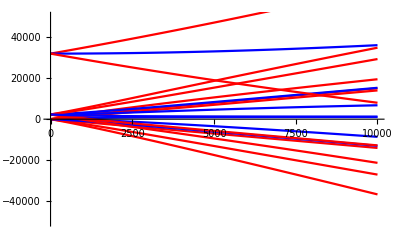

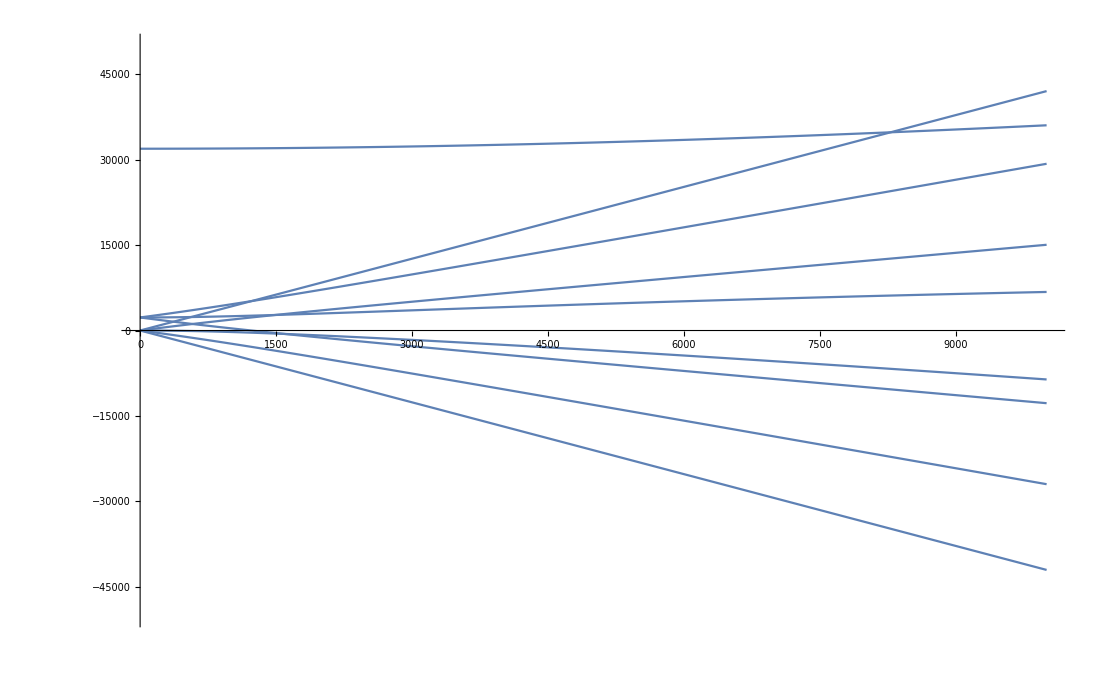

```mathematica
bvalues=Table[1+i 10,{i,0,1000}];
nv2sBs=Table[SetPrecision[{Δs->-192502669,gj->2.002237348,m->1.39962418,b->bvalues⟦i⟧},25],{i,Length[bvalues]}];
nv2pBs=Table[SetPrecision[{Em->-17085.298,Δp->-61431000,E0->31908.135,E1'->2291.173+4.75197,gs->2.002238867,gl->0.999873626,m->1.39962418,b->bvalues⟦i⟧},25],{i,Length[bvalues]}];

Pvs=Table[EigenSys[Hb+Ht3/.nv2pBs⟦i⟧],{i,Length[bvalues]}];
PBOrder=Table[Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,7,8,9,0,0,0} Transpose[Round[({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}}).Transpose[Pvs⟦b,2⟧]^2]]]⟦i⟧,Greater],{i,1,5}]],{{1},{13},{14},{25},{26},{27},{37},{38},{49}}],{b,1,Length[bvalues]}];
PLBOrder={1,6,2,9,7,3,8,4,5};
Pmap=Table[{Null,Null,Null,Null,Null,Null,Null,Null,Null},{b,1,Length[bvalues]}];
Do[Pmap⟦b,PLBOrder⟦i⟧⟧=PBOrder⟦b,i⟧,{b,1,Length[bvalues]},{i,1,9}];

Bdata2p=Table[Pvs⟦b,1,Pmap⟦b,i⟧⟧,{i,1,9},{b,1,Length[bvalues]}];
Bdata2s=Transpose[Table[Sort[Eigenvalues[H2s/.nv2sBs⟦i⟧]],{i,Length[bvalues]}]];
BdataTrans=Flatten[Table[Bdata2p⟦i⟧-Bdata2s⟦j⟧,{i,Length[Bdata2p]},{j,Length[Bdata2s]}],1];

SLevels={-1,0,1};
PLevels={-2,-1,0,1,2,-1,0,1,0};

Plots=Table[ListPlot[If[Abs[PLevels⟦i⟧-SLevels⟦j⟧]≤1,Table[{bvalues⟦b⟧,Bdata2p⟦i,b⟧-Bdata2s⟦j,b⟧},{b,Length[bvalues]}],{0,0}],Joined->True,DisplayFunction->Identity,PlotStyle->{RGBColor[If[Abs[PLevels⟦i⟧-SLevels⟦j⟧]==0,0,1],0,If[Abs[PLevels⟦i⟧-SLevels⟦j⟧]==0,1,0]]}],{i,1,9},{j,1,3}];
Show[Table[Plots⟦i⟧,{i,Length[Plots]}],PlotRange->{{0,10000},{-50000,50000}},DisplayFunction->$DisplayFunction]
Plots=Table[ListPlot[Table[{bvalues⟦b⟧,Bdata2p⟦i,b⟧},{b,Length[bvalues]}],Joined->True,DisplayFunction->Identity],{i,Length[Bdata2p]}];
Show[Table[Plots⟦i⟧,{i,Length[Plots]}],PlotRange->{{0,10000},{-50000,50000}},DisplayFunction->$DisplayFunction]
```

## Transition matrix elements for He-3

### For 2S states (2 singlets and 6 triplets): write Hamiltonian and diagonalize

#### Create operators, s1, s2 and Inuc.

```mathematica
s1=Table[spin⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2]),{i,1,3}];
s2=Table[IdentityMatrix[2]⊗(spin⟦i⟧⊗IdentityMatrix[2]),{i,1,3}];
Inuc=Table[IdentityMatrix[2]⊗(IdentityMatrix[2]⊗spin⟦i⟧),{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
Table[MatrixForm[Inuc⟦i⟧],{i,1,3}]
```

#### Introduce s1s2 interaction, change to S basis

```mathematica
s1s2=∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
S=s1+s2;
K=s1-s2;
H=Δs s1s2;
{Svals,Svecs}=EigenSys[H+b2 Inuc⟦3⟧+b1 S⟦3⟧/.{Δs->-100,b1->10,b2->1}];
S=Table[Svecs·S⟦i⟧·Transpose[Svecs],{i,1,3}];
K=Table[Svecs·K⟦i⟧·Transpose[Svecs],{i,1,3}];
Inuc=Table[Svecs·Inuc⟦i⟧·Transpose[Svecs],{i,1,3}];
HS=Svecs·H·Transpose[Svecs];
Table[MatrixForm[S⟦i⟧],{i,1,3}];
Table[MatrixForm[K⟦i⟧],{i,1,3}];
Table[MatrixForm[Inuc⟦i⟧],{i,1,3}];
MatrixForm[HS]
```

#### Change to F=S+I basis

```mathematica
nv2s=SetPrecision[{c2s->-4493.174543,c2s'->-3945.046,Δs->-192502669,gj->2.002237348,gi->0.00231748181,m->1.39962418,b->bvalue},25];
SInuc=∑_(i=1)^3 S⟦i⟧·Inuc⟦i⟧;
KInuc=∑_(i=1)^3 K⟦i⟧·Inuc⟦i⟧;
F=Inuc+S;
HF=HS+c2s SInuc-1/4 Δs IdentityMatrix[Length[HS]]+b F⟦3⟧;
{SvalF,SvecF}=EigenSys[HF/.{Δs->-100,c2s->-10,b->1}];
SvecsF=SvecF·Svecs;
Ft=Table[SvecF·F⟦i⟧·Transpose[SvecF],{i,1,3}];
Table[MatrixForm[Ft⟦i⟧],{i,1,3}];
Hb=m b (gi Inuc⟦3⟧+gj S⟦3⟧);
H=Hb+HS+c2s SInuc-1/4 Δs IdentityMatrix[Length[HS]]+c2s' KInuc;
Ht=Expand[Simplify[SvecF·H·Transpose[SvecF]]];
MatrixForm[Ht];
{SvalH,SvecH}=EigenSys[H/.nv2s];
E2s=SvalH;
BOrder=Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,0,0} Transpose[Round[{{1,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0},{0,0,0,1,1,0,0,0},{0,0,0,0,0,1,0,0}}.Transpose[SvecH^2]]]]⟦i⟧,Greater],{i,1,4}]],{{1},{9},{10},{17},{18},{25}}];
LBOrder={1,5,2,6,3,4};
Smf={Null,Null,Null,Null,Null,Null};
Do[Smf⟦LBOrder⟦i⟧⟧=BOrder⟦i⟧,{i,1,6}]
SvalH⟦5⟧-SvalH⟦1⟧;
SvecHs=SvecH·Svecs;
MatrixForm[N[Chop[SvecH·(H/.nv2s)·Transpose[SvecH],1/10^16],8]]
nv2sB=Table[SetPrecision[ReplacePart[nv2s,brange⟦i⟧,Length[nv2s]],Precision[nv2s]],{i,Length[brange]}];
E2sB=Table[Sort[Eigenvalues[H/.nv2sB⟦i⟧]],{i,Length[nv2sB]}];
TableForm[E2sB]
```

#### Display eigenvalues and slopes (gradient force) vs B

```mathematica
SHam=H;
bvalues=Table[i 1,{i,0,100}];
nv2s=Table[SetPrecision[{c2s->-4493.174543,c2s'->-3945.046,Δs->-192502669,gj->2.002237348,gi->.00231748181,m->1.39962418,b->bvalues⟦i⟧},25],{i,Length[bvalues]}];
Sval=Transpose[Table[Sort[Eigenvalues[H/.nv2s⟦i⟧]],{i,Length[bvalues]}]];
Svalt=Sval;
Sval⟦5⟧=Table[If[bvalues⟦b⟧>1600,Sval⟦5,b⟧=Svalt⟦4,b⟧,Sval⟦5,b⟧=Svalt⟦5,b⟧],{b,1,Length[bvalues]}];
Sval⟦4⟧=Table[If[bvalues⟦b⟧>1600,Sval⟦4,b⟧=Svalt⟦5,b⟧,Sval⟦4,b⟧=Svalt⟦4,b⟧],{b,1,Length[bvalues]}];
Svalslope=Table[(bvalues⟦b⟧ (Sval⟦i,b+1⟧-Sval⟦i,b⟧))/(bvalues⟦b+1⟧-bvalues⟦b⟧),{i,1,6},{b,Length[bvalues]-1}];
Svalslope=Append[Svalslope,Svalslope⟦3⟧+Svalslope⟦4⟧];
```

### For 2P states (6 singlets and 18 triplets): write Hamiltonian and diagonalize

#### Create operators, s1, s2, L2, and Inuc.

```mathematica
s1=Table[IdentityMatrix[3]⊗(spin⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2])),{i,1,3}];
s2=Table[IdentityMatrix[3]⊗(IdentityMatrix[2]⊗(spin⟦i⟧⊗IdentityMatrix[2])),{i,1,3}];L=Table[orbit⟦i⟧⊗(IdentityMatrix[2]⊗(IdentityMatrix[2]⊗IdentityMatrix[2])),{i,1,3}];
L2=Table[Ltensor⟦i⟧⊗(IdentityMatrix[2]⊗(IdentityMatrix[2]⊗IdentityMatrix[2])),{i,1,5}];
Inuc=Table[IdentityMatrix[3]⊗(IdentityMatrix[2]⊗(IdentityMatrix[2]⊗spin⟦i⟧)),{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
Lcor=Table[MatrixForm[L⟦i⟧],{i,1,3}];
Table[MatrixForm[L2⟦i⟧],{i,1,5}];
Table[MatrixForm[Inuc⟦i⟧],{i,1,3}]
```

#### Introduce interactions, change to S basis

```mathematica
s1s2=∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
{SvalP,SvecP}=EigenSys[s1s2 Δp+b3 Inuc⟦3⟧+b2 L⟦3⟧+b1 (s1⟦3⟧+s2⟦3⟧)/.{b1->10,b2->1,b3->1/10,Δp->-100}];
s1s2t=Simplify[SvecP·s1s2·Transpose[SvecP]];
S=Table[SvecP·(s1⟦i⟧+s2⟦i⟧)·Transpose[SvecP],{i,1,3}];
K=Table[SvecP·(s1⟦i⟧-s2⟦i⟧)·Transpose[SvecP],{i,1,3}];
Lt=Table[SvecP·L⟦i⟧·Transpose[SvecP],{i,1,3}];
L2t=Table[SvecP·L2⟦i⟧·Transpose[SvecP],{i,1,5}];
Inuct=Table[SvecP·Inuc⟦i⟧·Transpose[SvecP],{i,1,3}];
Table[MatrixForm[S⟦i⟧],{i,1,3}];
Table[MatrixForm[K⟦i⟧],{i,1,3}];
Lcort=Table[MatrixForm[Lt⟦i⟧],{i,1,3}];
Table[MatrixForm[L2t⟦i⟧],{i,1,5}];
Table[MatrixForm[Inuct⟦i⟧],{i,1,3}]
```

#### Change to J=L+S basis to introduce fine structure splittings, then transform back and include singlet-triplet mixing

```mathematica
LS=∑_(i=1)^3 S⟦i⟧·Lt⟦i⟧;
LK=∑_(i=1)^3 K⟦i⟧·Lt⟦i⟧;
J=Lt+S;
Hfs=ls LS+Δp s1s2t-1/4 Δp IdentityMatrix[Length[s1s2t]]+b3 Inuct⟦3⟧+b J⟦3⟧;
{Svalj,Svecj}=EigenSys[Hfs/.{Δp->-1000,ls->-100,b->10,b3->1}];
Jt=Table[Svecj·J⟦i⟧·Transpose[Svecj],{i,1,3}];
Table[MatrixForm[Jt⟦i⟧],{i,1,3}];
Hfst=DiagonalMatrix[{0,0,0,0,0,0,0,0,0,0,E1',E1',E1',E1',E1',E1',E0,E0,Δp,Δp,Δp,Δp,Δp,Δp}];
Hfs=(Em LK)/(√2)+Transpose[Svecj]·Hfst·Svecj;
MatrixForm[Hfs];
MatrixForm[Simplify[Svecj·Hfs·Transpose[Svecj]]]
```

#### Introduce hyperfine interactions

```mathematica
TripletOp=∑_(i=1)^3 S⟦i⟧·S⟦i⟧/2;
SingletOp=-TripletOp+IdentityMatrix[Length[TripletOp]];
LInuc=∑_(i=1)^3 Lt⟦i⟧·Inuct⟦i⟧;
SInuc=∑_(i=1)^3 S⟦i⟧·Inuct⟦i⟧;
KInuc=∑_(i=1)^3 K⟦i⟧·Inuct⟦i⟧;
SL2=2 √10 5 Table[∑_(q1=-2)^2 ∑_(q2=-1)^1 ClebschGordan[{2,q1},{1,q2},{1,m}] L2t⟦q1+3⟧·ir[S]⟦q2+2⟧,{m,-1,1}];
KL2=2 √10 5 Table[∑_(q1=-2)^2 ∑_(q2=-1)^1 ClebschGordan[{2,q1},{1,q2},{1,m}] L2t⟦q1+3⟧·ir[K]⟦q2+2⟧,{m,-1,1}];
TS=∑_(q=-1)^1 (-1)^q SL2⟦q+2⟧·ir[Inuct]⟦2-q⟧;
TK=∑_(q=-1)^1 (-1)^q KL2⟦q+2⟧·ir[Inuct]⟦2-q⟧;
Hb=m b (gI Inuct⟦3⟧+gl Lt⟦3⟧+gs S⟦3⟧);
H=Hb+Hfs+c1 KInuc+D LInuc·TripletOp+Ds LInuc·SingletOp+c SInuc-ϵ1 TK+ϵ TS;
H10=MatrixForm[Expand[H/.b->0]]
```

#### Find exact diagonalization transformation numerically for fine/hyperfine/mixing interaction

```mathematica
nv2p=SetPrecision[{E0->31908.135+.7133,E1'->2291.173+.9888+4.75197,e2->0.,Em->-17085.298,Δp->61431000,c->-4283.850+.0045,c1->-4285.8305,D->-28.145-.0017,Ds->-15.547,ϵ->(7.126+.0104)/5,ϵ1->5.597/5,gI->.00231748181,gs->2.002238867,gl->0.999834534,m->1.39962418,b->bvalue},35];
{SvalH,SvecH}=EigenSys[H/.nv2p];
SvecHP=SvecH·SvecP;
E2p=SvalH;
BOrder=Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,0,0,0,0,0,0} Transpose[Round[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}}.Transpose[SvecH^2]]]]⟦i⟧,Greater],{i,1,6}]],{{1},{25},{26},{27},{49},{50},{51},{52},{53},{73},{74},{75},{76},{77},{97},{98},{99},{121}}];
LBOrder={1,13,7,2,18,14,11,8,3,17,15,12,9,4,16,10,5,6};
Pmf={Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null};
Do[Pmf⟦LBOrder⟦i⟧⟧=BOrder⟦i⟧,{i,1,18}]
t1=MatrixForm[Chop[Simplify[SvecH·(H/.nv2p)·Transpose[SvecH]],1/10^16]]
nv2pB=Table[SetPrecision[ReplacePart[nv2p,brange⟦i⟧,Length[nv2p]],Precision[nv2p]],{i,Length[brange]}];
E2pB=Table[Sort[Eigenvalues[H/.nv2pB⟦i⟧]],{i,Length[nv2pB]}];
TableForm[E2pB];
PHam=H;
```

### Fit hfs constants

```mathematica
nv2p=SetPrecision[{E0->31908.135+.7133-.003,E1'->2291.173+.9888+4.75197+.002,e2->0.,Em->-17085.298,Δp->61431000,c->-4283.850+.0045+.0022,c1->-4285.8305,D->-28.145-.0017-.0074,Ds->-15.547,ϵ->1/5 (7.126+.0104-.0049),ϵ1->5.597/5,gI->.00231748181,gs->2.002238867,gl->0.999834534,m->1.39962418,b->bvalue},35];
{SvalH,SvecH}=EigenSys[H/.nv2p];
SvecHP=SvecH·SvecP;
E2p'=SvalH;
t1=MatrixForm[Chop[Simplify[SvecH·(H/.nv2p)·Transpose[SvecH]],1/10^16]];
trans35=(E2p'⟦7⟧-E2p'⟦1⟧)-(E2p⟦7⟧-E2p⟦1⟧)
trans13=(E2p'⟦11⟧-E2p'⟦7⟧)-(E2p⟦11⟧-E2p⟦7⟧)
trans31=(E2p'⟦13⟧-E2p'⟦11⟧)-(E2p⟦13⟧-E2p⟦11⟧)
trans01=(E2p'⟦17⟧-E2p'⟦11⟧)-(E2p⟦17⟧-E2p⟦11⟧)
```

```mathematica
sigma2=(.004)^2;trans35=0.0191;trans13=-0.0179;trans31=0.0009;trans01=0.0106;
FindMinimum[(.19 c+.79 d-2.56 e+.98 fs02-.98 fs12-trans01)^2/sigma2+(-.80 c-.08 d+3.98 e+.01 fs02+.29 fs12-trans13)^2/sigma2+(-.62 c+.71 d-2.18 e-.01 fs02-.68 fs12-trans31)^2/sigma2+(-.04 c-1.07 d-2.10 e+.00 fs02+.70 fs12-trans35)^2/sigma2/.{fs12->.00},{c,0},{d,0},{e,0},{fs02,0}]
```

### Transform electric dipole operator

create electric dipole operator in the |ed,ml,ms,mI> basis

```mathematica
edmsmlmI=Table[edm⟦i⟧⊗(IdentityMatrix[2]⊗(IdentityMatrix[2]⊗IdentityMatrix[2])),{i,1,3}];
Table[MatrixForm[edmsmlmI⟦i⟧],{i,1,3}];

Svec=ArrayFlatten[{{SvecHs,ConstantArray[0,{Length[SvecHs],Length[SvecHP]}]},{ConstantArray[0,{Length[SvecHP],Length[SvecHs]}],SvecHP}}];edH=Table[Svec·edmsmlmI⟦i⟧·Transpose[Svec],{i,1,3}];Table[MatrixForm[edH⟦i⟧],{i,1,3}];
t2=vec[edH];edHsq=N[Chop[Table[t2⟦i,j,k⟧ SuperStar[t2⟦i,j,k⟧],{i,1,3},{j,1,Length[t2⟦1⟧]},{k,1,Length[t2⟦1⟧]}],1/10^10],10];Table[MatrixForm[edHsq⟦i⟧],{i,1,3}]
```

### Determine rates into upper states, decay rates into other states, and signal size, repopulation rates, branching into detectable states, frequency

```mathematica
E2=Join[E2s+2246.5873,((.0141-.007)+810.599-.0011)+E2p-32232.7981];
Table[∑_(i=1)^3 ∑_(j=1)^32 edHsq⟦i,k,j⟧,{k,32}];
decay=Table[If[j==3||j==Smf⟦5⟧,1-∑_(p=1)^3 (edHsq⟦p,Pmf⟦i⟧+8,3⟧+edHsq⟦p,Pmf⟦i⟧+8,Smf⟦5⟧⟧),∑_(p=1)^3 (edHsq⟦p,Pmf⟦i⟧+8,3⟧+edHsq⟦p,Pmf⟦i⟧+8,Smf⟦5⟧⟧)],{i,1,18},{j,1,6}];
repopulateprob=Table[∑_(p=1)^3 edHsq⟦p,Pmf⟦i⟧+8,Smf⟦j⟧⟧,{i,1,18},{j,1,6}];
branching=Table[{(repopulateprob⟦i,1⟧+repopulateprob⟦i,2⟧)/(repopulateprob⟦i,1⟧+repopulateprob⟦i,2⟧+repopulateprob⟦i,4⟧+repopulateprob⟦i,6⟧),(repopulateprob⟦i,4⟧+repopulateprob⟦i,6⟧)/(repopulateprob⟦i,1⟧+repopulateprob⟦i,2⟧+repopulateprob⟦i,4⟧+repopulateprob⟦i,6⟧)},{i,1,18}];
t2=Table[{edHsq⟦3,Pmf⟦i⟧+8,Smf⟦j⟧⟧,edHsq⟦1,Pmf⟦i⟧+8,Smf⟦j⟧⟧,decay⟦i,Smf⟦j⟧⟧,(edHsq⟦1,Pmf⟦i⟧+8,Smf⟦j⟧⟧+edHsq⟦3,Pmf⟦i⟧+8,Smf⟦j⟧⟧) decay⟦i,Smf⟦j⟧⟧,(edHsq⟦1,Pmf⟦i⟧+8,Smf⟦j⟧⟧+edHsq⟦3,Pmf⟦i⟧+8,Smf⟦j⟧⟧) repopulateprob⟦i,j⟧,If[j==1,branching⟦i,1⟧,If[j==6,branching⟦i,2⟧,Null]],E2⟦Pmf⟦i⟧+8⟧-E2⟦Smf⟦j⟧⟧},{i,1,18},{j,1,6}];
Signal=Table[t2⟦i,j,k⟧,{i,18},{k,7},{j,6}];
NumberForm[TableForm[Signal,TableAlignments->Center,TableHeadings->{{"2,5/2;-5/2","2,5/2;-3/2","2,5/2;-1/2","2,5/2;+1/2","2,5/2;+3/2","2,5/2;+5/2","1,3/2;-3/2","1,3/2;-1/2","1,3/2;+1/2","1,3/2;+3/2","1,1/2;-1/2","1,1/2;+1/2","2,3/2;-3/2","2,3/2;-1/2","2,3/2;+1/2","2,3/2;+3/2","0,1/2;+1/2","0,1/2;-1/2"},{"              E||B","E⊥B","detectable decay","signal","repopulate","strong/weak","frequency"},{"(3/2;-3/2)   ","(3/2;-1/2)   ","(3/2;+1/2)   ","(3/2;+3/2)   ","(1/2;-1/2)   ","(1/2;+1/2)   "}}],{9,4}]
```

### Fit BField shifts

```mathematica
(*bvalues=Table[SetPrecision[b/.brange⟦i⟧,Precision[E2pB]],{i,Length[brange]}];
Bdata=Flatten[Table[{bvalues⟦i⟧,-If[bvalues⟦1⟧==0,E2pB⟦1,j⟧-E2sB⟦1,k⟧]+E2pB⟦i,j⟧-E2sB⟦i,k⟧},{j,Length[E2pB⟦1⟧]},{k,1,6},{i,Length[bvalues]}],1];
Btrans={102,100,101,99,98,108,107,105,104,103,96,95,93,90,89,88,87,86,84,82,81,80,79,76,74,73,72,71,70,69,68,66,64,63,62,61,60,59,57,54,53,52,51,50,48,46,45,44,43,40,38,37,30,29,27,24,23,22,21,20,18,16,15,14,13,10,8,7};
Bfit=Table[Fit[Bdata⟦Btrans⟦i⟧⟧,{B,B^2,B^3,B^4,B^5},B],{i,Length[Btrans]}];
TableForm[Bfit];
Blfit=Table[LinearFit[Bdata⟦Btrans⟦i⟧⟧,{1,2,3,4,5},b,ShowFit->False,ReturnResiduals->True],{i,Length[Btrans]}];
TableForm[Table[√((SumOfSquares/.Blfit⟦17 (i-1)+j⟧)/Length[bvalues]),{j,17},{i,4}]]*)

(* this only works in versions of mathematica that support the experimental data analysis package*)

(*Bdata⟦Btrans⟦1⟧⟧;
data = Bdata⟦Btrans⟦1⟧⟧[[All,2]];
Drop[data,1];
lm=LinearModelFit[Drop[Bdata⟦Btrans⟦1⟧⟧[[All,2]],1],{b,b^2,b^3,b^4,b^5},b,IncludeConstantBasis->False];
Normal[lm];
lm["Data"];
residlist=lm["FitResiduals"];
sumofsquares=∑_(i=1)^Length[residlist] residlist[[i]]^2;
lm["EstimatedVariance"];
lm["ANOVATable"];
lm["ANOVATableSumsOfSquares"][[6]];*)

(* test of workaround for the linear fit portion above *)
```

```mathematica
bvalues=Table[SetPrecision[b/.brange⟦i⟧,Precision[E2pB]],{i,Length[brange]}];
Bdata=Flatten[Table[{bvalues⟦i⟧,-If[bvalues⟦1⟧==0,E2pB⟦1,j⟧-E2sB⟦1,k⟧]+E2pB⟦i,j⟧-E2sB⟦i,k⟧},{j,Length[E2pB⟦1⟧]},{k,1,6},{i,Length[bvalues]}],1];
Btrans={102,100,101,99,98,108,107,105,104,103,96,95,93,90,89,88,87,86,84,82,81,80,79,76,74,73,72,71,70,69,68,66,64,63,62,61,60,59,57,54,53,52,51,50,48,46,45,44,43,40,38,37,30,29,27,24,23,22,21,20,18,16,15,14,13,10,8,7};
Bfit=Table[Fit[Bdata⟦Btrans⟦i⟧⟧,{B,B^2,B^3,B^4,B^5},B],{i,Length[Btrans]}];
TableForm[Bfit];
Blfit=Table[LinearModelFit[Drop[Bdata⟦Btrans⟦i⟧⟧[[All,2]],1],{b,b^2,b^3,b^4,b^5},b],{i,Length[Btrans]}];
TableForm[Table[√((Blfit⟦17 (i-1)+j⟧["ANOVATableSumsOfSquares"][[6]])/Length[bvalues]),{j,17},{i,4}]]
```

### Plot eigenvalues vs B

```mathematica
bvaluesPS=Table[1+i 100,{i,0,100}];
nv2s=Table[SetPrecision[{c2s->-4493.174543,c2s'->-3945.046,Δs->-192502669,gj->2.002237348,gi->.00231748181,m->1.39962418,b->bvaluesPS⟦i⟧},40],{i,Length[bvaluesPS]}];
Svs=Table[EigenSys[SHam/.nv2s⟦i⟧],{i,Length[bvaluesPS]}];
SBOrder=Table[Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,0,0} Transpose[Round[{{1,0,0,0,0,0,0,0},{0,1,1,0,0,0,0,0},{0,0,0,1,1,0,0,0},{0,0,0,0,0,1,0,0}}.Transpose[Svs⟦b,2⟧]^2]]]⟦i⟧,Greater],{i,1,4}]],{{1},{9},{10},{17},{18},{25}}],{b,1,Length[bvaluesPS]}];
SLBOrder={1,5,2,6,3,4};
Smap=Table[{Null,Null,Null,Null,Null,Null},{b,1,Length[bvaluesPS]}];
Do[Smap⟦b,SLBOrder⟦i⟧⟧=SBOrder⟦b,i⟧,{b,1,Length[bvaluesPS]},{i,1,6}];
nv2p=Table[SetPrecision[{E0->31908.135+.7133,E1'->2291.173+.9888+4.75197,e2->0.,Em->-17085.298,Δp->61431000,c->-4283.850+.0045,c1->-4285.8305,D->-28.145-.0017,Ds->-15.547,ϵ->(7.126+.0104)/5,ϵ1->5.597/5,gI->.00231748181,gs->2.002238867,gl->0.999834534,m->1.39962418,b->bvaluesPS⟦i⟧},40],{i,Length[bvaluesPS]}];
Pvs=Table[EigenSys[PHam/.nv2p⟦i⟧],{i,Length[bvaluesPS]}];
PBOrder=Table[Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,0,0,0,0,0,0} Transpose[Round[{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}}.Transpose[Pvs⟦b,2⟧]^2]]]⟦i⟧,Greater],{i,1,6}]],{{1},{25},{26},{27},{49},{50},{51},{52},{53},{73},{74},{75},{76},{77},{97},{98},{99},{121}}],{b,1,Length[bvaluesPS]}];
PLBOrder={1,13,7,2,18,14,11,8,3,17,15,12,9,4,16,10,5,6};
Pmap=Table[{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{b,1,Length[bvaluesPS]}];
Do[Pmap⟦b,PLBOrder⟦i⟧⟧=PBOrder⟦b,i⟧,{b,1,Length[bvaluesPS]},{i,1,18}];
SLevels={-3/2,-1/2,1/2,3/2,-1/2,1/2};
PLevels={-5/2,-3/2,-1/2,1/2,3/2,5/2,-3/2,-1/2,1/2,3/2,-1/2,1/2,-3/2,-1/2,1/2,3/2,1/2,-1/2};
Null
```

## View He-4 and He-3 Results

```mathematica
fr={0,2291.173,31908.135};
t1=Table[Plot[Evaluate[lorz[Signal⟦i,4,j⟧,Signal⟦i,7,j⟧,f+fr⟦fs⟧]],{f,-100,100},PlotRange->{0,.25},AspectRatio->1/5,AxesOrigin->{-12,0},DisplayFunction->Identity,PlotStyle->{RGBColor[If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,0,1],0,If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,1,0]],AbsoluteThickness[If[j==2,2,1]]}],{fs,1,3},{i,1,9},{j,1,3}];
Show[t1⟦1⟧,DisplayFunction->$DisplayFunction,PlotRange->{0,.25}]
Show[t1⟦2⟧,DisplayFunction->$DisplayFunction,PlotRange->{0,.25}]
Show[t1⟦3⟧,DisplayFunction->$DisplayFunction,PlotRange->{0,.25}]
```

```mathematica
minf=-200+810.6;
maxf=200+810.6;
t1=Table[Plot[Evaluate[lorz[Signal⟦i,4,j⟧,Signal⟦i,7,j⟧,f]],{f,minf,maxf},PlotRange->{0,.25},AspectRatio->1/3,DisplayFunction->Identity,PlotStyle->{RGBColor[If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,0,1],0,If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,1,0]],AbsoluteThickness[If[j==3||j==5,2,1]]}],{i,1,18},{j,1,6}];
Show[Table[t1⟦i,j⟧,{i,1,18},{j,1,6}],PlotRange->{{minf,maxf},{0,.25}},AxesOrigin->{minf,0},DisplayFunction->$DisplayFunction]
```

```mathematica
minf=-200-5929;
maxf=200-5929;
t1=Table[Plot[Evaluate[lorz[Signal⟦i,4,j⟧,Signal⟦i,7,j⟧,f]],{f,minf,maxf},PlotRange->{0,.25},AspectRatio->1/3,DisplayFunction->Identity,PlotStyle->{RGBColor[If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,0,1],0,If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,1,0]],AbsoluteThickness[If[j==3||j==5,2,1]]}],{i,1,18},{j,1,6}];
Show[Table[t1⟦i,j⟧,{i,1,18},{j,1,6}],PlotRange->{{minf,maxf},{0,.25}},AxesOrigin->{minf,0},DisplayFunction->$DisplayFunction]
```

```mathematica
tgu={{1,6},{7,10},{11,12},{13,16},{17,18}};tgl={{5,6},{1,4}};
t1=Table[Plot[Evaluate[lorz[Signal⟦i,4,j⟧,Signal⟦i,7,j⟧,f]],{f,fb0⟦Pmf⟦i⟧+8⟧-fb0⟦Smf⟦j⟧⟧-3000,fb0⟦Pmf⟦i⟧+8⟧-fb0⟦Smf⟦j⟧⟧+0},PlotRange->{0,.25},AspectRatio->1/3,AxesOrigin->{fb0⟦Pmf⟦i⟧+8⟧-fb0⟦Smf⟦j⟧⟧-125 0,0},DisplayFunction->Identity,PlotStyle->{RGBColor[If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,0,1],0,If[Signal⟦i,1,j⟧>Signal⟦i,2,j⟧,1,0]],AbsoluteThickness[If[j==3||j==5,2,1]]}],{i,1,18},{j,1,6}];
Table[Show[Table[t1⟦i,j⟧,{i,tgu⟦su,1⟧,tgu⟦su,2⟧},{j,tgl⟦sl,1⟧,tgl⟦sl,2⟧}],PlotRange->{0,.0025},DisplayFunction->$DisplayFunction],{su,5,1,-1},{sl,2,1,-1}]
```

# System of equations for J levels (don’t run)

## Initial actions

### import data from excel and build into list

##### import on lab system

```mathematica
s:=Import["C:\\Users\\jdp0364\\OneDrive - UNT System\\experimental data power vs survival.xlsx"]
s[[1]]//Grid
s[[2]]//Grid
s[[3]]//Grid
s[[4]]//Grid
s[[5]]//Grid
s[[6]]//Grid
glist=Partition[Drop[Flatten[s[[4]]],{19,20}],2]
plist=Drop[Flatten[glist],{2,-1,2}]
```

##### import on home system

```mathematica
s:=Import["D:\\halot\\Downloads\\experimental data power vs survival.xlsx"]
s[[1]]//Grid;
s[[2]]//Grid;
s[[3]]//Grid;
s[[4]]//Grid;
s[[5]]//Grid
s[[6]]//Grid
glist=s[[6]]
plist=Drop[Flatten[glist],{2,-1,2}]
```

Power (mW) | Survival | 
276.7 | 0.007 | 0.7
242.8 | 0.008 | 0.8
208.9 | 0.009 | 0.9
175. | 0.027 | 2.7
141.1 | 0.031 | 3.1
107.2 | 0.059 | 5.9
73.3 | 0.101 | 10.1
56.35 | 0.174 | 17.4
39.4 | 0.373 | 37.3
37.027 |  | 0.
22.9532 | 0.439 | 43.9
17.7702 | 0.641 | 64.1
10.7077 | 0.655 | 65.5
3.14681 | 0.928 | 92.8
0. | 1. | 100.

276.7 | 0.7
242.8 | 0.8
208.9 | 0.9
175. | 2.7
141.1 | 3.1
107.2 | 5.9
73.3 | 10.1
56.35 | 17.4
39.4 | 37.3
22.9532 | 43.9
17.7702 | 64.1
10.7077 | 65.5
3.14681 | 92.8
0. | 100.

{{276.7,0.7},{242.8,0.8},{208.9,0.9},{175.,2.7},{141.1,3.1},{107.2,5.9},{73.3,10.1},{56.35,17.4},{39.4,37.3},{22.9532,43.9},{17.7702,64.1},{10.7077,65.5},{3.14681,92.8},{0.,100.}}

{276.7,242.8,208.9,175.,141.1,107.2,73.3,56.35,39.4,22.9532,17.7702,10.7077,3.14681,0.}

### graph He^4 levels

```mathematica
TabView[{"Positive Pumping"-> GraphPlot[{{A<->D,"6"},{B<->"E","3"},{B<->"I","3"},{C<->F,"1"},{C<->J,"3"}},VertexLabeling->True,DirectedEdges->True,VertexCoordinates->{A-> {-1,0},B-> {0,0},C-> {1,0},D-> {-2,1},"E"-> {-1,1},F-> {0,1},G-> {1,1},H-> {2,1},"I"-> {-1,2},J-> {0,2},K-> {1,2}},PlotTheme->"Scientific"],"0 Pumping"-> GraphPlot[{{A<->"E","6"},{A<->"I","6"},{B<->F,"8"},{B<->J,"0"},{C<->G,"6"},{C->K,"6"}},VertexLabeling->True,DirectedEdges->True,VertexCoordinates->{A-> {-1,0},B-> {0,0},C-> {1,0},D-> {-2,1},"E"-> {-.8,1},F-> {0.2,1},G-> {1.2,1},H-> {2,1},"I"-> {-1,2},J-> {0,2},K-> {1,2}},PlotTheme->"Scientific"],"negative pumping"-> GraphPlot[{{A<->F,"1"},{A<->J,"3"},{B<->G,"3"},{B<->K,"3"},{C<->H,"6"}},VertexLabeling->True,DirectedEdges->True,VertexCoordinates->{A-> {-1,0},B-> {0,0},C-> {1,0},D-> {-2,1},"E"-> {-1,1},F-> {0,1},G-> {1,1},H-> {2,1},"I"-> {-1,2},J-> {0,2},K-> {1,2}},PlotTheme->"Scientific"],"Decays"-> GraphPlot[{{D->A,"6"},{"E"->A,"3"},{"E"->B,"3"},{F->A,"1"},{F->B,"4"},{F->C,"1"},{G->B,"3"},{H->C,"6"},{"I"->A,"3"},{"I"->B,"3"},{J->A,"3"},{J->C,"3"},{K->B,"3"},{K->C,"3"}},VertexLabeling->True,DirectedEdges->True,VertexCoordinates->{A-> {-1,0},B-> {0,0},C-> {1,0},D-> {-2,1},"E"-> {-1.2,1.2},F-> {0,1.4},G-> {1.2,1.2},H-> {2,1},"I"-> {-1.2,2},J-> {0,2},K-> {1.2,2}},PlotTheme->"Scientific"]}]
```

1234

### transition matrix requirements

Convert cartesian vectors into irreducible vectors

```mathematica
ir[v_]:={(v⟦1⟧-ⅈ v⟦2⟧)/(√2),v⟦3⟧,-(v⟦1⟧+ⅈ v⟦2⟧)/(√2)};
```

Convert irreducible vectors into cartesian vectors

```mathematica
vec[v_]:=Simplify[{(v⟦1⟧-v⟦3⟧)/(√2),(ⅈ (v⟦1⟧+v⟦3⟧))/(√2),v⟦2⟧}];
```

Lorentzian distribution function

```mathematica
lorz[int_,fr_,f_]:=int/(((f-fr)/(.8))^2+1);
```

Define operators for tensor direct product, complex conjugate, vector dot product and triple vector dot product

```mathematica
t1={{a,b},{c,d}}
t2={e,f}
t1.t2
```

{{a,b},{c,d}}

{e,f}

{a e+b f,c e+d f}

```mathematica
x_⊗y_:=ArrayFlatten[Outer[Times,x,y]];
SuperStar[x_]:=Conjugate[x];
x_·y_:=x.y;
x_·y_·z_:=x.y.z;
```

Defining a Module that returns eigenvalues and normalized eigenvectors sorted according to energy from low to high

```mathematica
Ordering[{1,2,√2},All,Less]
Ordering[{1,2,√2}]
```

{1,3,2}

{1,2,3}

```mathematica
EigenSys[op_]:=Module[{val,vect,sval,svect},{val,vect}=Eigensystem[op];vect=Table[vect⟦i⟧/(√(vect⟦i⟧.vect⟦i⟧)),{i,1,Length[vect]}];sval=Sort[val,Less];svect=vect⟦Ordering[val,All,Less]⟧;{sval,svect}]
```

```mathematica
M1={{4,0,0,0},{0,2,0,0},{0,0,√2,0},{0,0,0,1}}
EigenSys[M1]
```

{{4,0,0,0},{0,2,0,0},{0,0,√2,0},{0,0,0,1}}

{{1,√2,2,4},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}

### magnetic field value

```mathematica
bvalue=10;
brange=Table[b->i,{i,0,100,1}];
```

## Input basic operator building blocks

### Calculate electric dipole matrices (edm) corresponding to x - iy, z, and x + iy

```mathematica
ed=Simplify[Table[∫_0^π ∫_0^(2 π) SphericalHarmonicY[lf,mf,θ,-ϕ] √(4 π) SphericalHarmonicY[1,q,θ,ϕ] SphericalHarmonicY[li,mi,θ,ϕ] Sin[θ]ⅆϕⅆθ,{q,-1,1},{lf,0,1},{mf,-lf,lf},{li,0,1},{mi,-li,li}]];
edm=Table[Flatten[ed⟦i⟧],{i,1,3}];
Sq=√Length[edm⟦3⟧];
edm=Table[Table[edm⟦i⟧⟦r+(q-1)Sq⟧,{q,1,Sq},{r,1,Sq}],{i,1,3}];
Table[MatrixForm[edm⟦i⟧],{i,1,3}];
```

### Calculate orbital angular momentum tensor (Ltensor)

```mathematica
Ltensor=Simplify[Table[∫_0^π ∫_0^(2 π) SphericalHarmonicY[1,mf,θ,-ϕ] √((4 π)/5) SphericalHarmonicY[2,q,θ,ϕ] SphericalHarmonicY[1,mi,θ,ϕ] Sin[θ]ⅆϕⅆθ,{q,-2,2},{mf,-1,1},{mi,-1,1}]];
Table[MatrixForm[Ltensor⟦i⟧],{i,1,5}]
```

{(0 | 0 | -(√6)/5
0 | 0 | 0
0 | 0 | 0),(0 | (√3)/5 | 0
0 | 0 | -(√3)/5
0 | 0 | 0),(-1/5 | 0 | 0
0 | 2/5 | 0
0 | 0 | -1/5),(0 | 0 | 0
-(√3)/5 | 0 | 0
0 | (√3)/5 | 0),(0 | 0 | 0
0 | 0 | 0
-(√6)/5 | 0 | 0)}

### Construct the spin and orbit operators (spin, orbit)

```mathematica
spin=1/2{{{0,1},{1,0}},{{0,ⅈ},{-ⅈ,0}},{{-1,0},{0,1}}};
orbit={{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}},{{0,ⅈ/(√2),0},{-ⅈ/(√2),0,ⅈ/(√2)},{0,-ⅈ/(√2),0}},{{-1,0,0},{0,0,0},{0,0,1}}};

Table[MatrixForm[spin⟦i⟧],{i,1,3}];
Table[MatrixForm[ir[spin]⟦i⟧],{i,1,3}];
Table[MatrixForm[orbit⟦i⟧],{i,1,3}];
Table[MatrixForm[ir[orbit]⟦i⟧],{i,1,3}]
```

{(0 | 1 | 0
0 | 0 | 1
0 | 0 | 0),(-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1),(0 | 0 | 0
-1 | 0 | 0
0 | -1 | 0)}

## Transition matrix elements for He-4

### For 2S states (1 singlets and 3 triplets): write Hamiltonian and diagonalize

#### Create operators, s1 and s2.

Electron 1 spin operator(s1), electron 2 spin operator(s2)

```mathematica
s1=Table[spin⟦i⟧⊗IdentityMatrix[2],{i,1,3}];
s2=Table[IdentityMatrix[2]⊗spin⟦i⟧,{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
```

#### Introduce interactions, change to S basis

Δs = imperical singlet-triplet splitting parameter, gj = electron g-factor, m = Bohr magnaton, b = magnetic field value
s1s2 = spin-spin interaction operator, S = total spin operator, K = singlet-triplet mixing operator

```mathematica
nv2s=SetPrecision[{Δs->-192502669,gj->2.002237348,m->1.39962418,b->bvalue},17];
s1s2=Δs ∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
MatrixForm[s1s2];
S=s1+s2;
K=s1-s2;
H=s1s2-1/4 Δs IdentityMatrix[Length[s1s2]];
{Svals,Svecs}=EigenSys[s1s2+b S⟦3⟧/.{b->1,Δs->-10}];
Svals;
Svecs;
S=Table[Svecs·S⟦i⟧·Transpose[Svecs],{i,1,3}];
K=Table[Svecs·K⟦i⟧·Transpose[Svecs],{i,1,3}];
H=Svecs·H·Transpose[Svecs]+b gj m S⟦3⟧;
Table[MatrixForm[S⟦i⟧],{i,1,3}];
Table[MatrixForm[K⟦i⟧],{i,1,3}];
MatrixForm[H]
E2s=Sort[Eigenvalues[H/.nv2s]]
nv2sB=Table[SetPrecision[ReplacePart[nv2s,brange⟦i⟧,Length[nv2s]],Precision[nv2s]],{i,Length[brange]}];
E2sB=Table[Sort[Eigenvalues[H/.nv2sB⟦i⟧]],{i,Length[nv2sB]}];
TableForm[E2sB];
H2s=H;
```

(-b gj m | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | b gj m | 0
0 | 0 | 0 | -Δs)

{-28.02379806359875,0,28.02379806359875,1.92502669×10^8}

### For 2P states (3 singlets and 9 triplets): write Hamiltonian and diagonalize

#### Create operators, s1, s2, and L.

Electron 1 spin operator(s1), electron 2 spin operator(s2) and outer electron angular momentum operator(L)

```mathematica
s1=Table[IdentityMatrix[3]⊗(spin⟦i⟧⊗IdentityMatrix[2]),{i,1,3}];
s2=Table[IdentityMatrix[3]⊗(IdentityMatrix[2]⊗spin⟦i⟧),{i,1,3}];
L=Table[orbit⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2]),{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
Table[MatrixForm[L⟦i⟧],{i,1,3}];
```

#### Introduce spin-spin interactions, change to S basis

Spin-spin interatction operator(s1s2), total spin operator(S), singlet-triplet mixing operator(K)

```mathematica
s1s2=∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
S=s1+s2;
K=s1-s2;
H=Δp s1s2;
{Svalp,Svecp}=EigenSys[H+b1 L⟦3⟧+b2 S⟦3⟧/.{b1->1,b2->10,Δp->-100}];
St1=Table[Svecp·S⟦i⟧·Transpose[Svecp],{i,1,3}];
Kt1=Table[Svecp·K⟦i⟧·Transpose[Svecp],{i,1,3}];
Lt1=Table[Svecp·L⟦i⟧·Transpose[Svecp],{i,1,3}];
Ht1=Svecp·H·Transpose[Svecp];
Table[MatrixForm[St1⟦i⟧],{i,1,3}];
Table[MatrixForm[Kt1⟦i⟧],{i,1,3}];
Table[MatrixForm[Lt1⟦i⟧],{i,1,3}];
MatrixForm[Ht1]
```

(Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4)

#### Change to J = L + S basis

Em = (J=1) mixing, Δp = imperical s-t splitting parameter, E0 = ~ He4 0-2, E1' = He4 2-1 w/o s-t mixing, gs = electron g-factor, gl = orbital g-factor, m = Bohr magnaton, b = magnetic filed value
LS = spin-orbit interaction operator, LK = singlet-triplet-orbit interaction operator, J = total angular momentum operator

```mathematica
nvalues=SetPrecision[{Em->-17085.298,Δp->-61431000,E0->31908.135,E1'->2291.173+4.75197,gs->2.002238867,gl->0.999873626,m->1.39962418,b->bvalue},45];
LS=ls ∑_(i=1)^3 St1⟦i⟧·Lt1⟦i⟧;
LK=∑_(i=1)^3 Kt1⟦i⟧·Lt1⟦i⟧;
J=Lt1+St1;
{Svalj,Svecj}=EigenSys[Ht1+LS+b J⟦3⟧/.{Δp->-100,ls->-10,b->1}];
Svecjp=Svecj·Svecp;
Jt=Table[Svecj·J⟦i⟧·Transpose[Svecj],{i,1,3}];
LKt2=Svecj·LK·Transpose[Svecj];
Ht2=(Em LKt2)/(√2)+DiagonalMatrix[{0,0,0,0,0,E1',E1',E1',E0,0,0,0}]+Svecj·Ht1·Transpose[Svecj]-1/4 Δp IdentityMatrix[Length[Svecj]];
Ht3=Transpose[Svecj]·Ht2·Svecj;
Table[MatrixForm[Jt⟦i⟧],{i,1,3}];
MatrixForm[LKt2];
MatrixForm[Ht2];
MatrixForm[Ht3];
Hb=m b (gl Lt1⟦3⟧+gs St1⟦3⟧);
{SvalH,SvecH}=EigenSys[Hb+Ht3/.nvalues];
E2p=SvalH;
SvecHp=SvecH·Svecp;
PBOrder=Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,7,8,9,0,0,0} Transpose[Round[{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0}}.Transpose[SvecH]^2]]]⟦i⟧,Greater],{i,1,5}]],{{1},{13},{14},{25},{26},{27},{37},{38},{49}}];
PLBOrder={1,6,2,9,7,3,8,4,5};
Pmj={Null,Null,Null,Null,Null,Null,Null,Null,Null};
Do[Pmj⟦PLBOrder⟦i⟧⟧=PBOrder⟦i⟧,{i,1,9}];
MatrixForm[Chop[Simplify[SvecH·(Hb+Ht3/.nvalues)·Transpose[SvecH]],1/10^16]];
nv2pB=Table[SetPrecision[ReplacePart[nvalues,Length[nvalues]->brange⟦i⟧],Precision[nvalues]],{i,Length[brange]}];
E2pB=Table[Sort[Eigenvalues[Hb+Ht3/.nv2pB⟦i⟧]],{i,Length[nv2pB]}];
TableForm[E2pB];
```

### Transform electric dipole operator

```mathematica
edmsml=Table[edm⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2]),{i,1,3}];
Table[MatrixForm[edmsml⟦i⟧],{i,1,3}];
Svec=ArrayFlatten[{{Svecs,ConstantArray[0,{Length[Svecs],Length[Svecjp]}]},{ConstantArray[0,{Length[Svecjp],Length[Svecs]}],Svecjp}}];
edj=Table[Svec·edmsml⟦i⟧·Transpose[Svec],{i,1,3}];Table[MatrixForm[edj⟦i⟧],{i,1,3}];t1=vec[edj];
edsq=Table[t1⟦i,j,k⟧ SuperStar[t1⟦i,j,k⟧],{i,1,3},{j,1,Sq},{k,1,Sq}];Table[MatrixForm[edsq⟦i⟧],{i,1,3}];
Svec=ArrayFlatten[{{Svecs,ConstantArray[0,{Length[Svecs],Length[SvecHp]}]},{ConstantArray[0,{Length[SvecHp],Length[Svecs]}],SvecHp}}];
edH=Table[Svec·edmsml⟦i⟧·Transpose[Svec],{i,1,3}];Table[MatrixForm[edH⟦i⟧],{i,1,3}];t2=vec[edH];
edHsq=N[Chop[Table[t2⟦i,j,k⟧ SuperStar[t2⟦i,j,k⟧],{i,1,3},{j,1,Length[t2⟦1⟧]},{k,1,Length[t2⟦1⟧]}],1/10^10],10];
Column[Table[MatrixForm[edHsq⟦i⟧],{i,1,3}]]
```

(0 | 0 | 0 | 0 | 0.5 | 0 | 0.08435622939 | 0 | 0 | 0 | 0.2491349466 | 0 | 0.1665088047 | 0 | 1.933936094×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0.2484692249 | 0 | 0.2515307751 | 0 | 0.2515307557 | 0 | 0.2484692056 | 0 | 1.933936978×10^-8 | 0 | 1.933936978×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0.08231520137 | 0 | 0.5 | 0 | 0.2508601794 | 0 | 0.1668245999 | 0 | 1.933937861×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.867836821×10^-8 | 0 | 3.867838587×10^-8 | 0 | 0.4999999613 | 0 | 0.4999999613
0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692249 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.08435622939 | 0 | 0.08231520137 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307751 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307557 | 0 | 3.867836821×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.2491349466 | 0 | 0.2508601794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692056 | 0 | 3.867838587×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1665088047 | 0 | 0.1668245999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.933936094×10^-8 | 0 | 1.933937861×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0.5 | 0 | 0.08435622939 | 0 | 0 | 0 | 0.2491349466 | 0 | 0.1665088047 | 0 | 1.933936094×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0.2484692249 | 0 | 0.2515307751 | 0 | 0.2515307557 | 0 | 0.2484692056 | 0 | 1.933936978×10^-8 | 0 | 1.933936978×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0.08231520137 | 0 | 0.5 | 0 | 0.2508601794 | 0 | 0.1668245999 | 0 | 1.933937861×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.867836821×10^-8 | 0 | 3.867838587×10^-8 | 0 | 0.4999999613 | 0 | 0.4999999613
0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692249 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.08435622939 | 0 | 0.08231520137 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307751 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2515307557 | 0 | 3.867836821×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.2491349466 | 0 | 0.2508601794 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.2484692056 | 0 | 3.867838587×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1665088047 | 0 | 0.1668245999 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1.933936094×10^-8 | 0 | 1.933937861×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.933936978×10^-8 | 0 | 0.4999999613 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 0.5030615502 | 0 | 0 | 0 | 0.4969384111 | 0 | 0 | 0 | 3.867872189×10^-8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.6666571385 | 0 | 0 | 0 | 9.670622355×10^-6 | 0 | 0.3333331909 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0.5030615115 | 0 | 0 | 0 | 3.867875722×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0.9999999226 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5030615502 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.6666571385 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.4969384111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9.670622355×10^-6 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5030615115 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.3333331909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.867872189×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.867875722×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Determine rates into upper states, decay rates into other states, and signal size, repopulation rates, branching into detectable states, frequency

```mathematica
E2=Join[E2s,E2p];
Table[∑_(i=1)^3 ∑_(j=1)^16 edHsq⟦i,k,j⟧,{k,16}];
t1=Table[i,{i,5,13}];
t2=Table[{edHsq⟦3,Pmj⟦i⟧+4,j⟧,edHsq⟦1,Pmj⟦i⟧+4,j⟧,If[j==2,-2 edHsq⟦1,Pmj⟦i⟧+4,2⟧-edHsq⟦3,Pmj⟦i⟧+4,2⟧+1,2 edHsq⟦1,Pmj⟦i⟧+4,2⟧+edHsq⟦3,Pmj⟦i⟧+4,2⟧],(edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧) If[j==2,-2 edHsq⟦1,Pmj⟦i⟧+4,2⟧-edHsq⟦3,Pmj⟦i⟧+4,2⟧+1,2 edHsq⟦1,Pmj⟦i⟧+4,2⟧+edHsq⟦3,Pmj⟦i⟧+4,2⟧],(edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧) (2 edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧),If[j==2,Null,(2 edHsq⟦1,Pmj⟦i⟧+4,j⟧+edHsq⟦3,Pmj⟦i⟧+4,j⟧)/(2 edHsq⟦1,Pmj⟦i⟧+4,1⟧+2 edHsq⟦1,Pmj⟦i⟧+4,3⟧+edHsq⟦3,Pmj⟦i⟧+4,1⟧+edHsq⟦3,Pmj⟦i⟧+4,3⟧)],E2⟦Pmj⟦i⟧+4⟧-E2⟦j⟧},{i,1,9},{j,1,3}];
Signal=Table[t2⟦i,j,k⟧,{i,9},{k,7},{j,3}];
NumberForm[TableForm[Signal,TableAlignments->Center,TableHeadings->{t1,{"          E||B","E⊥B","decay","signal","repopulate","branching","frequency"},{"(1;-1)   ","(1;0)   ","(1;+1)   "}}],{8,4}]
```

|           E||B | E⊥B | decay | signal | repopulate | branching | frequency
5 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0.5000
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 1
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0.5000
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 1.0000
(1;0)    | Null
(1;+1)    | 0 | (1;-1)    | -13.9945
(1;0)    | -42.0183
(1;+1)    | -70.0421
6 | (1;-1)    | 0.5031
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0.2485
(1;+1)    | 0 | (1;-1)    | 0.4969
(1;0)    | 0.5031
(1;+1)    | 0.4969 | (1;-1)    | 0.2500
(1;0)    | 0.1250
(1;+1)    | 0 | (1;-1)    | 0.2531
(1;0)    | 0.1235
(1;+1)    | 0 | (1;-1)    | 1.0000
(1;0)    | Null
(1;+1)    | 0 | (1;-1)    | 6.9932
(1;0)    | -21.0306
(1;+1)    | -49.0544
7 | (1;-1)    | 0
(1;0)    | 0.6667
(1;+1)    | 0 | (1;-1)    | 0.0844
(1;0)    | 0
(1;+1)    | 0.0823 | (1;-1)    | 0.6667
(1;0)    | 0.3333
(1;+1)    | 0.6667 | (1;-1)    | 0.0562
(1;0)    | 0.2222
(1;+1)    | 0.0549 | (1;-1)    | 0.0142
(1;0)    | 0.4444
(1;+1)    | 0.0136 | (1;-1)    | 0.5061
(1;0)    | Null
(1;+1)    | 0.4939 | (1;-1)    | 27.9952
(1;0)    | -0.0286
(1;+1)    | -28.0524
8 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.4969 | (1;-1)    | 0
(1;0)    | 0.2515
(1;+1)    | 0 | (1;-1)    | 0.5031
(1;0)    | 0.4969
(1;+1)    | 0.5031 | (1;-1)    | 0
(1;0)    | 0.1250
(1;+1)    | 0.2500 | (1;-1)    | 0
(1;0)    | 0.1265
(1;+1)    | 0.2469 | (1;-1)    | 0
(1;0)    | Null
(1;+1)    | 1.0000 | (1;-1)    | 49.0115
(1;0)    | 20.9877
(1;+1)    | -7.0361
9 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.5000 | (1;-1)    | 0
(1;0)    | 1
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.5000 | (1;-1)    | 0
(1;0)    | Null
(1;+1)    | 1.0000 | (1;-1)    | 70.0421
(1;0)    | 42.0183
(1;+1)    | 13.9945
10 | (1;-1)    | 0.4969
(1;0)    | 0
(1;+1)    | 0 | (1;-1)    | 0
(1;0)    | 0.2515
(1;+1)    | 0 | (1;-1)    | 0.5031
(1;0)    | 0.4969
(1;+1)    | 0.5031 | (1;-1)    | 0.2500
(1;0)    | 0.1250
(1;+1)    | 0 | (1;-1)    | 0.2469
(1;0)    | 0.1265
(1;+1)    | 0 | (1;-1)    | 1.0000
(1;0)    | Null
(1;+1)    | 0 | (1;-1)    | 2298.2091
(1;0)    | 2270.1853
(1;+1)    | 2242.1615
11 | (1;-1)    | 0
(1;0)    | 9.6706×10^-6
(1;+1)    | 0 | (1;-1)    | 0.2491
(1;0)    | 0
(1;+1)    | 0.2509 | (1;-1)    | 9.6706×10^-6
(1;0)    | 1.0000
(1;+1)    | 9.6706×10^-6 | (1;-1)    | 2.4093×10^-6
(1;0)    | 9.6705×10^-6
(1;+1)    | 2.4260×10^-6 | (1;-1)    | 0.1241
(1;0)    | 9.3521×10^-11
(1;+1)    | 0.1259 | (1;-1)    | 0.4983
(1;0)    | Null
(1;+1)    | 0.5017 | (1;-1)    | 2319.2210
(1;0)    | 2291.1972
(1;+1)    | 2263.1734
12 | (1;-1)    | 0
(1;0)    | 0
(1;+1)    | 0.5031 | (1;-1)    | 0
(1;0)    | 0.2485
(1;+1)    | 0 | (1;-1)    | 0.4969
(1;0)    | 0.5031
(1;+1)    | 0.4969 | (1;-1)    | 0
(1;0)    | 0.1250
(1;+1)    | 0.2500 | (1;-1)    | 0
(1;0)    | 0.1235
(1;+1)    | 0.2531 | (1;-1)    | 0
(1;0)    | Null
(1;+1)    | 1.0000 | (1;-1)    | 2340.2274
(1;0)    | 2312.2036
(1;+1)    | 2284.1798
13 | (1;-1)    | 0
(1;0)    | 0.3333
(1;+1)    | 0 | (1;-1)    | 0.1665
(1;0)    | 0
(1;+1)    | 0.1668 | (1;-1)    | 0.3333
(1;0)    | 0.6667
(1;+1)    | 0.3333 | (1;-1)    | 0.0555
(1;0)    | 0.2222
(1;+1)    | 0.0556 | (1;-1)    | 0.0555
(1;0)    | 0.1111
(1;+1)    | 0.0557 | (1;-1)    | 0.4995
(1;0)    | Null
(1;+1)    | 0.5005 | (1;-1)    | 31936.1630
(1;0)    | 31908.1390
(1;+1)    | 31880.1160

### Fit BField shifts

```mathematica
bvalues=Table[SetPrecision[b/.brange⟦i⟧,Precision[E2pB]],{i,Length[brange]}];
Bdata=Flatten[Table[{bvalues⟦i⟧,E2pB⟦i,j⟧-E2sB⟦i,k⟧-If[bvalues⟦1⟧==0,E2pB⟦1,j⟧-E2sB⟦1,1⟧]},{j,Length[E2pB⟦1⟧]},{k,3},{i,Length[bvalues]}],1];
Btrans={27,26,25,24,23,21,19,17,16,12,11,9,8,7,5,4};
Bfit=Table[Fit[Bdata⟦Btrans⟦i⟧⟧,{B,B^2,B^3,B^4},B],{i,Length[Btrans]}];
TableForm[Bfit]
Blfit=Table[LinearFit[Bdata⟦Btrans⟦i⟧⟧,{1,2,3,4},b],{i,Length[Btrans]}];
```

-2.80237980636219 B+0.0000443040134830225 B^2-2.47072588631506×10^-15 B^3-3.55029501214596×10^-14 B^4
-7.242550285637759172836285018342869×10^-14 B+0.00004430401335001056590123669292057667 B^2-1.673914048254348201565341515866077×10^-16 B^3-3.551511276652015936202763686401377×10^-14 B^4
2.80237980635926 B+0.0000443040133786227 B^2-6.29824009731113×10^-16 B^3-3.55127833428274×10^-14 B^4
-0.70146524947134 B+0.00021476237281314 B^2-1.6162374246804×10^-11 B^3-1.998564417027×10^-11 B^4
2.100914556888641867189808091521543285426 B+0.0002147623728068088834291594004207755026214 B^2-1.616226607618960839302327166282908122203×10^-11 B^3-1.99856447352637223414698197984829565557×10^-11 B^4
-2.8023798194276 B+0.000242046143731847 B^2-3.02336697282163×10^-11 B^3-3.03416127354131×10^-11 B^4
2.80237979329336 B+0.000242046143657579 B^2-3.02323530265286×10^-11 B^3-3.03416198053896×10^-11 B^4
-2.100914570866773101837879124921527643772 B+0.0002147623728087202428876454421669920297961 B^2-1.617249526073321588788984195299011788549×10^-11 B^3-1.998564405004928857188464630164351246333×10^-11 B^4
0.7014652354931 B+0.00021476237280841 B^2-1.6172487194364×10^-11 B^3-1.9985644103068×10^-11 B^4
-0.70146518122906 B-0.00021476237282595 B^2+1.6162563195771×10^-11 B^3+1.9985643212322×10^-11 B^4
2.100914625130495662380493646096552492383311 B-0.0002147623728080481583094255391379297624981174 B^2+1.616226607616130584547622337073764580864855×10^-11 B^3+1.998564473526372234082344296062374652459816×10^-11 B^4
-2.80237979329238 B-0.00028635015706171 B^2+3.02333970364107×10^-11 B^3+3.03771303429373×10^-11 B^4
1.306688469972563154114347514869855071892189×10^-8 B-0.0002863501570315425066581562945724927462202471 B^2+3.023293481008538957264710692494616737856209×10^-11 B^3+3.037713257175766391467207115283271805614538×10^-11 B^4
2.8023798194279 B-0.000286350157099849 B^2+3.02341250310275×10^-11 B^3+3.03771262642258×10^-11 B^4
-2.100914611152364427732422612696568132781893 B-0.0002147623728099595177679115808641794340370974 B^2+1.617249526076151843543689024798338848019325×10^-11 B^3+1.998564405004928857123827658349912451251781×10^-11 B^4
0.70146519520745 B-0.00021476237280622 B^2+1.6172431089874×10^-11 B^3+1.9985644387283×10^-11 B^4

### Plot eigenvalues vs B

-Graphics-

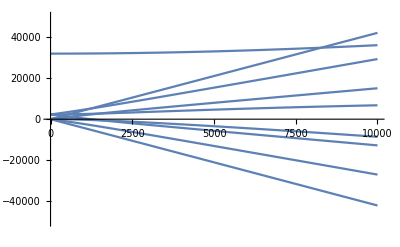

```mathematica
bvalues=Table[1+i 10,{i,0,1000}];
nv2sBs=Table[SetPrecision[{Δs->-192502669,gj->2.002237348,m->1.39962418,b->bvalues⟦i⟧},25],{i,Length[bvalues]}];
nv2pBs=Table[SetPrecision[{Em->-17085.298,Δp->-61431000,E0->31908.135,E1'->2291.173+4.75197,gs->2.002238867,gl->0.999873626,m->1.39962418,b->bvalues⟦i⟧},25],{i,Length[bvalues]}];

Pvs=Table[EigenSys[Hb+Ht3/.nv2pBs⟦i⟧],{i,Length[bvalues]}];
PBOrder=Table[Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,7,8,9,0,0,0} Transpose[Round[({{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1, 0, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}}).Transpose[Pvs⟦b,2⟧]^2]]]⟦i⟧,Greater],{i,1,5}]],{{1},{13},{14},{25},{26},{27},{37},{38},{49}}],{b,1,Length[bvalues]}];
PLBOrder={1,6,2,9,7,3,8,4,5};
Pmap=Table[{Null,Null,Null,Null,Null,Null,Null,Null,Null},{b,1,Length[bvalues]}];
Do[Pmap⟦b,PLBOrder⟦i⟧⟧=PBOrder⟦b,i⟧,{b,1,Length[bvalues]},{i,1,9}];

Bdata2p=Table[Pvs⟦b,1,Pmap⟦b,i⟧⟧,{i,1,9},{b,1,Length[bvalues]}];
Bdata2s=Transpose[Table[Sort[Eigenvalues[H2s/.nv2sBs⟦i⟧]],{i,Length[bvalues]}]];
BdataTrans=Flatten[Table[Bdata2p⟦i⟧-Bdata2s⟦j⟧,{i,Length[Bdata2p]},{j,Length[Bdata2s]}],1];

SLevels={-1,0,1};
PLevels={-2,-1,0,1,2,-1,0,1,0};

Plots=Table[ListPlot[If[Abs[PLevels⟦i⟧-SLevels⟦j⟧]≤1,Table[{bvalues⟦b⟧,Bdata2p⟦i,b⟧-Bdata2s⟦j,b⟧},{b,Length[bvalues]}],{0,0}],Joined->True,DisplayFunction->Identity,PlotStyle->{RGBColor[If[Abs[PLevels⟦i⟧-SLevels⟦j⟧]==0,0,1],0,If[Abs[PLevels⟦i⟧-SLevels⟦j⟧]==0,1,0]]}],{i,1,9},{j,1,3}];
Show[Table[Plots⟦i⟧,{i,Length[Plots]}],PlotRange->{{0,10000},{-50000,50000}},DisplayFunction->$DisplayFunction]
Plots=Table[ListPlot[Table[{bvalues⟦b⟧,Bdata2p⟦i,b⟧},{b,Length[bvalues]}],Joined->True,DisplayFunction->Identity],{i,Length[Bdata2p]}];
Show[Table[Plots⟦i⟧,{i,Length[Plots]}],PlotRange->{{0,10000},{-50000,50000}},DisplayFunction->$DisplayFunction]
```

## system

### corrected linear pumping coefficients

```mathematica
ExperimentalPoints:={{276.7,3.4020618556701034},{242.8,3.7113402061855676},{208.9,4.226804123711339},{175.,4.742268041237113},{141.1,5.876288659793814},{107.2,7.628865979381443},{73.3,12.164948453608247},{56.35,14.742268041237114},{39.4,23.4020618556701},{37.027,33.4020618556701},{22.95319149,34.22680412371133},{17.77021277,37.7319587628866},{10.70769231,60.618556701030926},{3.146808511,84.63917525773196},{0.,100.}}
(* list of experimental data {powerleve(mW),Survival of 0 channel} *)
powerlist=Drop[Flatten[ExperimentalPoints],{2,-1,2}];
(* list of power levels to check *)
(* powerlist:=Drop[Flatten[ExperimentalPoints],{2,-1,2}] *)(* method for taking the ExperimentalPoints list & using it to make the powerlist *)
testlista:={}
(* empty list for -1 channel values *)
testlistb:={}
(* empty list for zero channel values *)
testlistc:={}
(* empty list for +1 channel values *)
testlistd:={}
testliste:={}
testlistf:={}
testlistg:={}
testlisth:={}
testlisti:={}
testlistj:={}
testlistk:={}
θ :=0.1
(* alignment angle *)
v:=1364
(*He^4 Subscript[V, rms]*)
dd:=6*10^-3
(*apperature length used to calculate interaction time*)
interactiontimelist:={}
For[i=1,i≤ Length[powerlist],i++,r=2π *1.6*10^6;
kk=5.8*10^3*5.362/6;
(*pumping power scaling factor -> adjust to match 0 channel value to experimental data *)
pi=powerlist[[i]] kk;
(* pumping power *)
pp=pi((1+Cos[θ])/2)^2;
(*positive pumping*)
p0=pi ((Sin[θ])^2/2);
(*0 pumping*)
pn=pi ((1-Cos[θ])/2)^2;
(*negative pumping*)
tf=dd/v;
(*interaction time*)
sc=1;
s=NDSolve[{a'[t]==-pp a[t]-3pp a[t]+pp f[t]+3pp j[t]-6p0 a[t]-6p0 a[t]+6p0 e[t]+6p0 ii[t]-6pn a[t]+6pn d[t]+6/6 r d[t]+3/6 r e[t]+1/6 r f[t]+3/6 r ii[t]+3/6 r j[t],b'[t]==-3pp b[t]-3pp b[t]+3pp g[t]+3pp k[t]-4p0 b[t]+4p0 f[t]-3pn b[t]-3pn b[t]+3pn e[t]+3pn ii[t]+3/6 r e[t]+4/6 r f[t]+3/6 r g[t]+3/6 r ii[t]+3/6 r k[t], c'[t]== -6pp c[t]+6pp h[t]-6p0 c[t]-6p0 c[t]+6p0 g[t]+6p0 k[t]-pn c[t]-3pn c[t]+pn f[t]+3pn j[t]+1/6 r f[t]+3/6 r g[t]+6/6 r h[t]+3/6 r j[t]+3/6 r k[t],
d'[t]== -6pn d[t]+6pn a[t]-6/6 r d[t],
 e'[t]==-6p0 e[t]+6p0 a[t]-3pn e[t]+3pn b[t]-3/6 r e[t]-3/6 r e[t],f'[t]==-pp f[t]+pp a[t]-4p0 f[t]+4p0 b[t]-pn f[t]+pn c[t]-1/6 r f[t]-4/6 r f[t]-1/6 r f[t],g'[t]==-3pp g[t]+3pp b[t]-6p0 g[t]+6p0 c[t]-3/6 r g[t]-3/6 r g[t],
h'[t]==-6pp h[t]+6 pp c[t]-6/6 r h[t],
ii'[t]==-6p0 ii[t]+6p0 a[t]-3pn ii[t]+3pn b[t]-3/6 r ii[t]-3/6 r ii[t],
j'[t]==-3pp j[t]+3pp a[t]-3pn j[t]+3pn c[t]-3/6 r j[t]-3/6 r j[t],
k'[t]==-3pp k[t]+3pp b[t]-6p0 k[t]+6p0 c[t]-3/6 r k[t]-3/6 r k[t],
a[0]==100,b[0]==100,c[0]==100,d[0]==0,e[0]==0,f[0]==0,g[0]==0,h[0]==0,ii[0]==0,j[0]==0,k[0]==0},{a,b,c,d,e,f,g,h,ii,j,k},{t,0,sc*tf},PrecisionGoal-> 500,AccuracyGoal->11];
AppendTo[testlista,a[sc*tf]/.s];
AppendTo[testlistb,b[sc*tf]/.s];
AppendTo[testlistc,c[sc*tf]/.s];
AppendTo[testlistd,d[sc*tf]/.s];
AppendTo[testliste,e[sc*tf]/.s];
AppendTo[testlistf,f[sc*tf]/.s];
AppendTo[testlistg,g[sc*tf]/.s];
AppendTo[testlisth,h[sc*tf]/.s];
AppendTo[testlisti,ii[sc*tf]/.s];
AppendTo[testlistj,j[sc*tf]/.s];
AppendTo[testlistk,k[sc*tf]/.s];
AppendTo[interactiontimelist,tf]]

testlistflat:=Flatten[testlistb]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistb:=Riffle[powerlist,testlistflat]
(* combine the powerlist and flattened testlist *)


testlistaflat:=Flatten[testlista]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlista:=Riffle[powerlist,testlistaflat]
(* combine the powerlist and flattened testlist *)


testlistcflat:=Flatten[testlistc]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistc:=Riffle[powerlist,testlistcflat]
(* combine the powerlist and flattened testlist *)


testlistdflat:=Flatten[testlistd]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistd:=Riffle[powerlist,testlistdflat]
(* combine the powerlist and flattened testlist *)


testlisteflat:=Flatten[testliste]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedliste:=Riffle[powerlist,testlisteflat]
(* combine the powerlist and flattened testlist *)


testlistfflat:=Flatten[testlistf]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistf:=Riffle[powerlist,testlistfflat]
(* combine the powerlist and flattened testlist *)


testlistgflat:=Flatten[testlistg]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistg:=Riffle[powerlist,testlistgflat]
(* combine the powerlist and flattened testlist *)


testlisthflat:=Flatten[testlisth]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlisth:=Riffle[powerlist,testlisthflat]
(* combine the powerlist and flattened testlist *)


testlistiflat:=Flatten[testlisti]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlisti:=Riffle[powerlist,testlistiflat]
(* combine the powerlist and flattened testlist *)


testlistjflat:=Flatten[testlistj]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistj:=Riffle[powerlist,testlistjflat]
(* combine the powerlist and flattened testlist *)


testlistkflat:=Flatten[testlistk]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistk:=Riffle[powerlist,testlistkflat]
(* combine the powerlist and flattened testlist *)


data=Partition[riffedlistb,2];
model = α Exp[- β t]+γ;
fit= FindFit[data,model,{α,β,γ},t];
modelf=Function[{t},Evaluate[model /. fit]];
FITPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,data]},PlotRange->{{0,300},{0,100}},PlotLabel-> "model fit"];


model = α1 Exp[- β1 t]+γ1;
fit= FindFit[ExperimentalPoints,model,{α1,β1,γ1},t];
modelf=Function[{t},Evaluate[model /. fit]];
EXPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,ExperimentalPoints]},PlotRange->{{0,300},{0,100}},PlotLabel-> "Experimental data fit"];

TabView[{TabView[{a->ListPlot[{Partition[riffedlista,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → -1 channel"],b->ListPlot[{Partition[riffedlistb,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → 0 channel"],c->ListPlot[{Partition[riffedlistc,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → +1 channel"],d->ListPlot[{Partition[riffedlistd,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → d level"],e->ListPlot[{Partition[riffedliste,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → e level"],f->ListPlot[{Partition[riffedlistf,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → f level"],g->ListPlot[{Partition[riffedlistg,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → g level"],h->ListPlot[{Partition[riffedlisth,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → h level"],"i"->ListPlot[{Partition[riffedlisti,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → i level"],j->ListPlot[{Partition[riffedlistj,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → j level"],k->ListPlot[{Partition[riffedlistk,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → k level"]},2],TabView[{a->MatrixForm[Partition[riffedlista,2]],b->MatrixForm[Partition[riffedlistb,2]] ,c->MatrixForm[Partition[riffedlistc,2]] ,d->MatrixForm[Partition[riffedlistd,2]],e->MatrixForm[Partition[riffedliste,2]] ,f->MatrixForm[Partition[riffedlistf,2]],g->MatrixForm[Partition[riffedlistg,2] ],h->MatrixForm[Partition[riffedlisth,2]],"i"->MatrixForm[Partition[riffedlisti,2]],j->MatrixForm[Partition[riffedlistj,2]],k->MatrixForm[Partition[riffedlistk,2]] ,"Experimental Values"-> MatrixForm[ExperimentalPoints]},2],TabView[{"Model Fit"-> FITPlot,"Experimental data fit"->EXPlot}]}]
```

123

# use values from matrix for system of equations

## Initial actions

### transition matrix requirements

Convert cartesian vectors into irreducible vectors

```mathematica
ir[v_]:={(v⟦1⟧-ⅈ v⟦2⟧)/(√2),v⟦3⟧,-(v⟦1⟧+ⅈ v⟦2⟧)/(√2)};
```

Convert irreducible vectors into cartesian vectors

```mathematica
vec[v_]:=Simplify[{(v⟦1⟧-v⟦3⟧)/(√2),(ⅈ (v⟦1⟧+v⟦3⟧))/(√2),v⟦2⟧}];
```

Lorentzian distribution function

```mathematica
lorz[int_,fr_,f_]:=int/(((f-fr)/(.8))^2+1);
```

Define operators for tensor direct product, complex conjugate, vector dot product and triple vector dot product

```mathematica
t1={{a,b},{c,d}}
t2={e,f}
t1.t2
```

{{a,b},{c,d}}

{e,f}

{a e+b f,c e+d f}

```mathematica
x_⊗y_:=ArrayFlatten[Outer[Times,x,y]];
SuperStar[x_]:=Conjugate[x];
x_·y_:=x.y;
x_·y_·z_:=x.y.z;
```

Defining a Module that returns eigenvalues and normalized eigenvectors sorted according to energy from low to high

```mathematica
Ordering[{1,2,√2},All,Less]
Ordering[{1,2,√2}]
```

{1,3,2}

{1,2,3}

```mathematica
EigenSys[op_]:=Module[{val,vect,sval,svect},{val,vect}=Eigensystem[op];vect=Table[vect⟦i⟧/(√(vect⟦i⟧.vect⟦i⟧)),{i,1,Length[vect]}];sval=Sort[val,Less];svect=vect⟦Ordering[val,All,Less]⟧;{sval,svect}]
```

```mathematica
M1={{4,0,0,0},{0,2,0,0},{0,0,√2,0},{0,0,0,1}}
EigenSys[M1]
```

{{4,0,0,0},{0,2,0,0},{0,0,√2,0},{0,0,0,1}}

{{1,√2,2,4},{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}}}

### magnetic field value

```mathematica
bvalue=1;
brange=Table[b->i,{i,0,100,1}];
```

## Input basic operator building blocks

### Calculate electric dipole matrices (edm) corresponding to x - iy, z, and x + iy

```mathematica
ed=Simplify[Table[∫_0^π ∫_0^(2 π) SphericalHarmonicY[lf,mf,θ,-ϕ] √(4 π) SphericalHarmonicY[1,q,θ,ϕ] SphericalHarmonicY[li,mi,θ,ϕ] Sin[θ]ⅆϕⅆθ,{q,-1,1},{lf,0,1},{mf,-lf,lf},{li,0,1},{mi,-li,li}]];
edm=Table[Flatten[ed⟦i⟧],{i,1,3}];
Sq=√Length[edm⟦3⟧];
edm=Table[Table[edm⟦i⟧⟦r+(q-1)Sq⟧,{q,1,Sq},{r,1,Sq}],{i,1,3}];
Table[MatrixForm[edm⟦i⟧],{i,1,3}];
```

### Calculate orbital angular momentum tensor (Ltensor)

```mathematica
Ltensor=Simplify[Table[∫_0^π ∫_0^(2 π) SphericalHarmonicY[1,mf,θ,-ϕ] √((4 π)/5) SphericalHarmonicY[2,q,θ,ϕ] SphericalHarmonicY[1,mi,θ,ϕ] Sin[θ]ⅆϕⅆθ,{q,-2,2},{mf,-1,1},{mi,-1,1}]];
Table[MatrixForm[Ltensor⟦i⟧],{i,1,5}]
```

{(0 | 0 | -(√6)/5
0 | 0 | 0
0 | 0 | 0),(0 | (√3)/5 | 0
0 | 0 | -(√3)/5
0 | 0 | 0),(-1/5 | 0 | 0
0 | 2/5 | 0
0 | 0 | -1/5),(0 | 0 | 0
-(√3)/5 | 0 | 0
0 | (√3)/5 | 0),(0 | 0 | 0
0 | 0 | 0
-(√6)/5 | 0 | 0)}

### Construct the spin and orbit operators (spin, orbit)

```mathematica
spin=1/2{{{0,1},{1,0}},{{0,ⅈ},{-ⅈ,0}},{{-1,0},{0,1}}};
orbit={{{0,1/(√2),0},{1/(√2),0,1/(√2)},{0,1/(√2),0}},{{0,ⅈ/(√2),0},{-ⅈ/(√2),0,ⅈ/(√2)},{0,-ⅈ/(√2),0}},{{-1,0,0},{0,0,0},{0,0,1}}};

Table[MatrixForm[spin⟦i⟧],{i,1,3}];
Table[MatrixForm[ir[spin]⟦i⟧],{i,1,3}];
Table[MatrixForm[orbit⟦i⟧],{i,1,3}];
Table[MatrixForm[ir[orbit]⟦i⟧],{i,1,3}]
```

{(0 | 1 | 0
0 | 0 | 1
0 | 0 | 0),(-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1),(0 | 0 | 0
-1 | 0 | 0
0 | -1 | 0)}

## Transition matrix elements for He-4

### For 2S states (1 singlets and 3 triplets): write Hamiltonian and diagonalize

#### Create operators, s1 and s2.

Electron 1 spin operator(s1), electron 2 spin operator(s2)

```mathematica
s1=Table[spin⟦i⟧⊗IdentityMatrix[2],{i,1,3}];
s2=Table[IdentityMatrix[2]⊗spin⟦i⟧,{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
```

#### Introduce interactions, change to S basis

Δs = imperical singlet-triplet splitting parameter, gj = electron g-factor, m = Bohr magnaton, b = magnetic field value
s1s2 = spin-spin interaction operator, S = total spin operator, K = singlet-triplet mixing operator

```mathematica
nv2s=SetPrecision[{Δs->-192502669,gj->2.002237348,m->1.39962418,b->bvalue},17];
s1s2=Δs ∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
MatrixForm[s1s2];
S=s1+s2;
K=s1-s2;
H=s1s2-1/4 Δs IdentityMatrix[Length[s1s2]];
{Svals,Svecs}=EigenSys[s1s2+b S⟦3⟧/.{b->1,Δs->-10}];
Svals;
Svecs;
S=Table[Svecs·S⟦i⟧·Transpose[Svecs],{i,1,3}];
K=Table[Svecs·K⟦i⟧·Transpose[Svecs],{i,1,3}];
H=Svecs·H·Transpose[Svecs]+b gj m S⟦3⟧;
Table[MatrixForm[S⟦i⟧],{i,1,3}];
Table[MatrixForm[K⟦i⟧],{i,1,3}];
MatrixForm[H]
E2s=Sort[Eigenvalues[H/.nv2s]]
nv2sB=Table[SetPrecision[ReplacePart[nv2s,brange⟦i⟧,Length[nv2s]],Precision[nv2s]],{i,Length[brange]}];
E2sB=Table[Sort[Eigenvalues[H/.nv2sB⟦i⟧]],{i,Length[nv2sB]}];
TableForm[E2sB];
H2s=H;
```

(-b gj m | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | b gj m | 0
0 | 0 | 0 | -Δs)

{-28.02379806359875,0,28.02379806359875,1.92502669×10^8}

### For 2P states (3 singlets and 9 triplets): write Hamiltonian and diagonalize

#### Create operators, s1, s2, and L.

Electron 1 spin operator(s1), electron 2 spin operator(s2) and outer electron angular momentum operator(L)

```mathematica
s1=Table[IdentityMatrix[3]⊗(spin⟦i⟧⊗IdentityMatrix[2]),{i,1,3}];
s2=Table[IdentityMatrix[3]⊗(IdentityMatrix[2]⊗spin⟦i⟧),{i,1,3}];
L=Table[orbit⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2]),{i,1,3}];
Table[MatrixForm[s1⟦i⟧],{i,1,3}];
Table[MatrixForm[s2⟦i⟧],{i,1,3}];
Table[MatrixForm[L⟦i⟧],{i,1,3}];
```

#### Introduce spin-spin interactions, change to S basis

Spin-spin interatction operator(s1s2), total spin operator(S), singlet-triplet mixing operator(K)

```mathematica
s1s2=∑_(i=1)^3 s1⟦i⟧·s2⟦i⟧;
S=s1+s2;
K=s1-s2;
H=Δp s1s2;
{Svalp,Svecp}=EigenSys[H+b1 L⟦3⟧+b2 S⟦3⟧/.{b1->1,b2->10,Δp->-100}];
St1=Table[Svecp·S⟦i⟧·Transpose[Svecp],{i,1,3}];
Kt1=Table[Svecp·K⟦i⟧·Transpose[Svecp],{i,1,3}];
Lt1=Table[Svecp·L⟦i⟧·Transpose[Svecp],{i,1,3}];
Ht1=Svecp·H·Transpose[Svecp];
Table[MatrixForm[St1⟦i⟧],{i,1,3}];
Table[MatrixForm[Kt1⟦i⟧],{i,1,3}];
Table[MatrixForm[Lt1⟦i⟧],{i,1,3}];
MatrixForm[Ht1]
```

(Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | Δp/4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -(3 Δp)/4)

#### Change to J = L + S basis

Em = (J=1) mixing, Δp = imperical s-t splitting parameter, E0 = ~ He4 0-2, E1' = He4 2-1 w/o s-t mixing, gs = electron g-factor, gl = orbital g-factor, m = Bohr magnaton, b = magnetic filed value
LS = spin-orbit interaction operator, LK = singlet-triplet-orbit interaction operator, J = total angular momentum operator

```mathematica
nvalues=SetPrecision[{Em->-17085.298,Δp->-61431000,E0->31908.135,E1'->2291.173+4.75197,gs->2.002238867,gl->0.999873626,m->1.39962418,b->bvalue},45];
LS=ls ∑_(i=1)^3 St1⟦i⟧·Lt1⟦i⟧;
LK=∑_(i=1)^3 Kt1⟦i⟧·Lt1⟦i⟧;
J=Lt1+St1;
{Svalj,Svecj}=EigenSys[Ht1+LS+b J⟦3⟧/.{Δp->-100,ls->-10,b->1}];
Svecjp=Svecj·Svecp;
Jt=Table[Svecj·J⟦i⟧·Transpose[Svecj],{i,1,3}];
LKt2=Svecj·LK·Transpose[Svecj];
Ht2=(Em LKt2)/(√2)+DiagonalMatrix[{0,0,0,0,0,E1',E1',E1',E0,0,0,0}]+Svecj·Ht1·Transpose[Svecj]-1/4 Δp IdentityMatrix[Length[Svecj]];
Ht3=Transpose[Svecj]·Ht2·Svecj;
Table[MatrixForm[Jt⟦i⟧],{i,1,3}];
MatrixForm[LKt2];
MatrixForm[Ht2];
MatrixForm[Ht3];
Hb=m b (gl Lt1⟦3⟧+gs St1⟦3⟧);
{SvalH,SvecH}=EigenSys[Hb+Ht3/.nvalues];
E2p=SvalH;
SvecHp=SvecH·Svecp;
PBOrder=Extract[Flatten[Table[Sort[Transpose[{1,2,3,4,5,6,7,8,9,0,0,0} Transpose[Round[{{1,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0}}.Transpose[SvecH]^2]]]⟦i⟧,Greater],{i,1,5}]],{{1},{13},{14},{25},{26},{27},{37},{38},{49}}];
PLBOrder={1,6,2,9,7,3,8,4,5};
Pmj={Null,Null,Null,Null,Null,Null,Null,Null,Null};
Do[Pmj⟦PLBOrder⟦i⟧⟧=PBOrder⟦i⟧,{i,1,9}];
MatrixForm[Chop[Simplify[SvecH·(Hb+Ht3/.nvalues)·Transpose[SvecH]],1/10^16]];
nv2pB=Table[SetPrecision[ReplacePart[nvalues,Length[nvalues]->brange⟦i⟧],Precision[nvalues]],{i,Length[brange]}];
E2pB=Table[Sort[Eigenvalues[Hb+Ht3/.nv2pB⟦i⟧]],{i,Length[nv2pB]}];
TableForm[E2pB];
```

### Transform electric dipole operator

```mathematica
edmsml=Table[edm⟦i⟧⊗(IdentityMatrix[2]⊗IdentityMatrix[2]),{i,1,3}];
Table[MatrixForm[edmsml⟦i⟧],{i,1,3}];
Svec=ArrayFlatten[{{Svecs,ConstantArray[0,{Length[Svecs],Length[Svecjp]}]},{ConstantArray[0,{Length[Svecjp],Length[Svecs]}],Svecjp}}];
edj=Table[Svec·edmsml⟦i⟧·Transpose[Svec],{i,1,3}];Table[MatrixForm[edj⟦i⟧],{i,1,3}];t1=vec[edj];
edsq=Table[t1⟦i,j,k⟧ SuperStar[t1⟦i,j,k⟧],{i,1,3},{j,1,Sq},{k,1,Sq}];Table[MatrixForm[edsq⟦i⟧],{i,1,3}];
Svec=ArrayFlatten[{{Svecs,ConstantArray[0,{Length[Svecs],Length[SvecHp]}]},{ConstantArray[0,{Length[SvecHp],Length[Svecs]}],SvecHp}}];
edH=Table[Svec·edmsml⟦i⟧·Transpose[Svec],{i,1,3}];Table[MatrixForm[edH⟦i⟧],{i,1,3}];t2=vec[edH];
edHsq=N[Chop[Table[t2⟦i,j,k⟧ SuperStar[t2⟦i,j,k⟧],{i,1,3},{j,1,Length[t2⟦1⟧]},{k,1,Length[t2⟦1⟧]}],1/10^10],10];
Table[MatrixForm[edHsq⟦i⟧],{i,1,3}];
edHredsq=N[Chop[Table[edH⟦i,j,k⟧ SuperStar[edH⟦i,j,k⟧],{i,1,3},{j,1,Length[t2⟦1⟧]},{k,1,Length[t2⟦1⟧]}],1/10^10],10];
Column[Table[MatrixForm[edHredsq⟦i⟧],{i,1,3}]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0.1687124588 | 0 | 0 | 0 | 0.4982698932 | 0 | 0.3330176093 | 0 | 3.867872188×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5030615502 | 0 | 0 | 0 | 0.4969384111 | 0 | 0 | 0 | 3.867873956×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735677175×10^-8 | 0 | 0 | 0 | 0.9999999226
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.4969384498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1646304027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5030615115 | 0 | 7.735673641×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5017203588 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.3336491998 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.867873956×10^-8 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.867875723×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 0 | 0.5030615502 | 0 | 0 | 0 | 0.4969384111 | 0 | 0 | 0 | 3.867872189×10^-8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.6666571385 | 0 | 0 | 0 | 9.670622355×10^-6 | 0 | 0.3333331909 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0.5030615115 | 0 | 0 | 0 | 3.867875722×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0.9999999226 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5030615502 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.6666571385 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.4969384111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9.670622355×10^-6 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5030615115 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.3333331909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.867872189×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.867875722×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)
(0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0.5030615115 | 0 | 0 | 0 | 3.867873956×10^-8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1646304027 | 0 | 0 | 0 | 0.5017203588 | 0 | 0.3336491998 | 0 | 3.867875723×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735673641×10^-8 | 0 | 0 | 0 | 0.9999999226 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1687124588 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5030615502 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.4982698932 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.4969384111 | 0 | 7.735677175×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.3330176093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.867872188×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.867873956×10^-8 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### define the matrix called for populating pumping coefficient list

```mathematica
matrixelements:=Table[edHredsq⟦i⟧,{i,1,3}]
MatrixForm[matrixelements[[1]]]
MatrixForm[matrixelements[[2]]]
MatrixForm[matrixelements[[3]]]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0.1687124588 | 0 | 0 | 0 | 0.4982698932 | 0 | 0.3330176093 | 0 | 3.867872188×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.5030615502 | 0 | 0 | 0 | 0.4969384111 | 0 | 0 | 0 | 3.867873956×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735677175×10^-8 | 0 | 0 | 0 | 0.9999999226
1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.4969384498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.1646304027 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5030615115 | 0 | 7.735673641×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5017203588 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.3336491998 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.867873956×10^-8 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.867875723×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0.5030615502 | 0 | 0 | 0 | 0.4969384111 | 0 | 0 | 0 | 3.867872189×10^-8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.6666571385 | 0 | 0 | 0 | 9.670622355×10^-6 | 0 | 0.3333331909 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0.5030615115 | 0 | 0 | 0 | 3.867875722×10^-8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0.9999999226 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5030615502 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.6666571385 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.4969384111 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9.670622355×10^-6 | 0 | 7.735650083×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.5030615115 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.3333331909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.867872189×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3.867875722×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.4969384498 | 0 | 0 | 0 | 0.5030615115 | 0 | 0 | 0 | 3.867873956×10^-8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.1646304027 | 0 | 0 | 0 | 0.5017203588 | 0 | 0.3336491998 | 0 | 3.867875723×10^-8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 7.735673641×10^-8 | 0 | 0 | 0 | 0.9999999226 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.1687124588 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.5030615502 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.4982698932 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.4969384111 | 0 | 7.735677175×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.3330176093 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3.867872188×10^-8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3.867873956×10^-8 | 0 | 0.9999999226 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

## system (if system is evaluated need to quit kernel before running matrix cells or it breaks them)

### previous (don’t run)

#### pumping coefficients from matrix

fiat

```mathematica
ppaf:=1
ppaj:=3
ppbg:=3
ppbk:=3
ppch:=6
(* right circular polarized pumping *)
p0ae:=6
p0ai:=6
p0bf:=4
p0cg:=6
p0ck:=6
(* linear polarized pumping *)
pnad:=6
pnbe:=3
pnbi:=3
pncf:=1
pncj:=3
(* left circular polarized pumping *)
```

from matrix b=1

```mathematica
ppaf:=matrixelements[[1,1,7]]
ppaj:=matrixelements[[1,1,11]]
ppbg:=matrixelements[[1,2,8]]
ppbk:=matrixelements[[1,2,12]]
ppch:=matrixelements[[1,3,9]]
(* right circular polarized pumping *)
p0ae:=matrixelements[[2,1,6]]
p0ai:=matrixelements[[2,1,10]]
p0bf:=matrixelements[[2,2,7]]
p0cg:=matrixelements[[2,3,8]]
p0ck:=matrixelements[[2,3,12]]
(* linear polarized pumping *)
pnad:=matrixelements[[3,1,5]]
pnbe:=matrixelements[[3,2,6]]
pnbi:=matrixelements[[3,2,10]]
pncf:=matrixelements[[3,3,7]]
pncj:=matrixelements[[3,3,11]]
(* left circular polarized pumping *)
```

#### system using defined pumping coefficients from matrix

```mathematica
(* rework this into a function that can be called; set pumping coefficients as a list function takes as parameter; might need to use Module command *)
ExperimentalPoints:={{276.7,0.7000000000000001},{242.8,0.8},{208.9,0.8999999999999999},{175.,2.7},{141.1,3.1},{107.2,5.8999999999999995},{73.3,10.100000000000001},{56.35,17.4},{39.4,37.3},{22.95319149,43.9},{17.77021277,64.1},{10.70769231,65.5},{3.146808511,92.80000000000001},{0.,100.}}
(* list of experimental data {powerleve(mW),Survival of 0 channel} *)
powerlist=Drop[Flatten[ExperimentalPoints],{2,-1,2}];
(* list of power levels to check *)
(* powerlist:=Drop[Flatten[ExperimentalPoints],{2,-1,2}] *)(* method for taking the ExperimentalPoints list & using it to make the powerlist *)
testlista:={}
(* empty list for -1 channel values *)
testlistb:={}
(* empty list for zero channel values *)
testlistc:={}
(* empty list for +1 channel values *)
testlistd:={}
testliste:={}
testlistf:={}
testlistg:={}
testlisth:={}
testlisti:={}
testlistj:={}
testlistk:={}
θ :=0.073
(* alignment angle *)
v:=1364
(*He^4 Subscript[V, rms]*)
dd:=6*10^-3
(*apperature length used to calculate interaction time*)
For[i=1,i≤ Length[powerlist],i++,r=2π *1.6*10^6;
kk=5.8*10^3*2;
(*pumping power scaling factor -> adjust to match 0 channel value to experimental data *)
pi=powerlist[[i]] kk;
(* pumping power *)
pp=pi((1+Cos[θ])/2)^2;
(*positive pumping*)
p0=pi ((Sin[θ])^2/2);
(*0 pumping*)
pn=pi ((1-Cos[θ])/2)^2;
(*negative pumping*)
tf=dd/v;
(*interaction time*)
sc=1;
s=NDSolve[{a'[t]==-ppaf pp a[t]-ppaj pp a[t]+ppaf pp f[t]+ppaj pp j[t]-p0ae p0 a[t]-p0ai p0 a[t]+p0ae p0 e[t]+p0ai p0 ii[t]-pnad pn a[t]+pnad pn d[t]+6/6 r d[t]+3/6 r e[t]+1/6 r f[t]+3/6 r ii[t]+3/6 r j[t],b'[t]==-ppbg pp b[t]-ppbk pp b[t]+ppbg pp g[t]+ppbk pp k[t]-p0bf p0 b[t]+p0bf p0 f[t]-pnbe pn b[t]-pnbi pn b[t]+pnbe pn e[t]+pnbi pn ii[t]+3/6 r e[t]+4/6 r f[t]+3/6 r g[t]+3/6 r ii[t]+3/6 r k[t], c'[t]== -ppch pp c[t]+ppch pp h[t]-p0cg p0 c[t]-p0ck p0 c[t]+p0cg p0 g[t]+p0ck p0 k[t]-pncf pn c[t]-pncj pn c[t]+pncf pn f[t]+pncj pn j[t]+1/6 r f[t]+3/6 r g[t]+6/6 r h[t]+3/6 r j[t]+3/6 r k[t],
d'[t]== -pnad pn d[t]+pnad pn a[t]-6/6 r d[t],
 e'[t]==-p0ae p0 e[t]+p0ae p0 a[t]-pnbe pn e[t]+pnbe pn b[t]-3/6 r e[t]-3/6 r e[t],f'[t]==-ppaf pp f[t]+ppaf pp a[t]-p0bf p0 f[t]+p0bf p0 b[t]-pncf pn f[t]+pncf pn c[t]-1/6 r f[t]-4/6 r f[t]-1/6 r f[t],g'[t]==-ppbg pp g[t]+ppbg pp b[t]-p0cg p0 g[t]+p0cg p0 c[t]-3/6 r g[t]-3/6 r g[t],
h'[t]==-ppch pp h[t]+ppch pp c[t]-6/6 r h[t],
ii'[t]==-p0ai p0 ii[t]+p0ai p0 a[t]-pnbi pn ii[t]+pnbi pn b[t]-3/6 r ii[t]-3/6 r ii[t],
j'[t]==-ppaj pp j[t]+ppaj pp a[t]-pncj pn j[t]+pncj pn c[t]-3/6 r j[t]-3/6 r j[t],
k'[t]==-ppbk pp k[t]+ppbk pp b[t]-p0ck p0 k[t]+p0ck p0 c[t]-3/6 r k[t]-3/6 r k[t],
a[0]==100,b[0]==100,c[0]==100,d[0]==0,e[0]==0,f[0]==0,g[0]==0,h[0]==0,ii[0]==0,j[0]==0,k[0]==0},{a,b,c,d,e,f,g,h,ii,j,k},{t,0,sc*tf},PrecisionGoal-> 500,AccuracyGoal->11];
AppendTo[testlista,a[sc*tf]/.s];
AppendTo[testlistb,b[sc*tf]/.s];
AppendTo[testlistc,c[sc*tf]/.s];
AppendTo[testlistd,d[sc*tf]/.s];
AppendTo[testliste,e[sc*tf]/.s];
AppendTo[testlistf,f[sc*tf]/.s];
AppendTo[testlistg,g[sc*tf]/.s];
AppendTo[testlisth,h[sc*tf]/.s];
AppendTo[testlisti,ii[sc*tf]/.s];
AppendTo[testlistj,j[sc*tf]/.s];
AppendTo[testlistk,k[sc*tf]/.s]]

testlistflat:=Flatten[testlistb]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistb:=Riffle[powerlist,testlistflat]
(* combine the powerlist and flattened testlist *)


testlistaflat:=Flatten[testlista]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlista:=Riffle[powerlist,testlistaflat]
(* combine the powerlist and flattened testlist *)


testlistcflat:=Flatten[testlistc]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistc:=Riffle[powerlist,testlistcflat]
(* combine the powerlist and flattened testlist *)


testlistdflat:=Flatten[testlistd]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistd:=Riffle[powerlist,testlistdflat]
(* combine the powerlist and flattened testlist *)


testlisteflat:=Flatten[testliste]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedliste:=Riffle[powerlist,testlisteflat]
(* combine the powerlist and flattened testlist *)


testlistfflat:=Flatten[testlistf]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistf:=Riffle[powerlist,testlistfflat]
(* combine the powerlist and flattened testlist *)


testlistgflat:=Flatten[testlistg]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistg:=Riffle[powerlist,testlistgflat]
(* combine the powerlist and flattened testlist *)


testlisthflat:=Flatten[testlisth]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlisth:=Riffle[powerlist,testlisthflat]
(* combine the powerlist and flattened testlist *)


testlistiflat:=Flatten[testlisti]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlisti:=Riffle[powerlist,testlistiflat]
(* combine the powerlist and flattened testlist *)


testlistjflat:=Flatten[testlistj]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistj:=Riffle[powerlist,testlistjflat]
(* combine the powerlist and flattened testlist *)


testlistkflat:=Flatten[testlistk]
(* flatten the testlist into a list of values instead of a list of lists *)
riffedlistk:=Riffle[powerlist,testlistkflat]
(* combine the powerlist and flattened testlist *)


data=Partition[riffedlistb,2];
model = α Exp[- β t]+γ;
fit= FindFit[data,model,{α,β,γ},t];
modelf=Function[{t},Evaluate[model /. fit]];
FITPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,data]},PlotRange->{{0,300},{0,100}},PlotLabel-> "model fit"];


model = α1 Exp[- β1 t]+γ1;
fit= FindFit[ExperimentalPoints,model,{α1,β1,γ1},t];
modelf=Function[{t},Evaluate[model /. fit]];
EXPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,ExperimentalPoints]},PlotRange->{{0,300},{0,100}},PlotLabel-> "Experimental data fit"];

TabView[{TabView[{a->ListPlot[{Partition[riffedlista,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → -1 channel"],b->ListPlot[{Partition[riffedlistb,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → 0 channel"],c->ListPlot[{Partition[riffedlistc,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → +1 channel"],d->ListPlot[{Partition[riffedlistd,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → d level"],e->ListPlot[{Partition[riffedliste,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → e level"],f->ListPlot[{Partition[riffedlistf,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → f level"],g->ListPlot[{Partition[riffedlistg,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → g level"],h->ListPlot[{Partition[riffedlisth,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → h level"],"i"->ListPlot[{Partition[riffedlisti,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → i level"],j->ListPlot[{Partition[riffedlistj,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → j level"],k->ListPlot[{Partition[riffedlistk,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → k level"]},2],TabView[{a->MatrixForm[Partition[riffedlista,2]],b->MatrixForm[Partition[riffedlistb,2]] ,c->MatrixForm[Partition[riffedlistc,2]] ,d->MatrixForm[Partition[riffedlistd,2]],e->MatrixForm[Partition[riffedliste,2]] ,f->MatrixForm[Partition[riffedlistf,2]],g->MatrixForm[Partition[riffedlistg,2] ],h->MatrixForm[Partition[riffedlisth,2]],"i"->MatrixForm[Partition[riffedlisti,2]],j->MatrixForm[Partition[riffedlistj,2]],k->MatrixForm[Partition[riffedlistk,2]] ,"Experimental Values"-> MatrixForm[ExperimentalPoints]},2],TabView[{"Model Fit"-> FITPlot,"Experimental data fit"->EXPlot}]},2]
```

123

#### test

```mathematica
(* rework this into a function that can be called; set pumping coefficients as a list function takes as parameter; might need to use Module command *)
ExperimentalPoints:={{276.7,0.7000000000000001},{242.8,0.8},{208.9,0.8999999999999999},{175.,2.7},{141.1,3.1},{107.2,5.8999999999999995},{73.3,10.100000000000001},{56.35,17.4},{39.4,37.3},{22.95319149,43.9},{17.77021277,64.1},{10.70769231,65.5},{3.146808511,92.80000000000001},{0.,100.}}
(* list of experimental data {powerleve(mW),Survival of 0 channel} *)
powerlist=Drop[Flatten[ExperimentalPoints],{2,-1,2}];
(* list of power levels to check *)
(* powerlist:=Drop[Flatten[ExperimentalPoints],{2,-1,2}] *)(* method for taking the ExperimentalPoints list & using it to make the powerlist *)
testlista:={}
testlistb:={}
testlistc:={}
testlistd:={}
testliste:={}
testlistf:={}
testlistg:={}
testlisth:={}
testlisti:={}
testlistj:={}
testlistk:={}
θ :=0.073
(* alignment angle *)
v:=1364
(*He^4 Subscript[V, rms]*)
dd:=6*10^-3
(*apperature length used to calculate interaction time*)
For[i=1,i≤ Length[powerlist],i++,r=2π *1.6*10^6;
kk=5.8*10^3*2;
(*pumping power scaling factor -> adjust to match 0 channel value to experimental data *)
pi=powerlist[[i]] kk;
(* pumping power *)
pp=pi((1+Cos[θ])/2)^2;
(*positive pumping*)
p0=pi ((Sin[θ])^2/2);
(*0 pumping*)
pn=pi ((1-Cos[θ])/2)^2;
(*negative pumping*)
tf=dd/v;
(*interaction time*)
sc=1;
s=NDSolve[{a'[t]==-ppaf pp a[t]-ppaj pp a[t]+ppaf pp f[t]+ppaj pp j[t]-p0ae p0 a[t]-p0ai p0 a[t]+p0ae p0 e[t]+p0ai p0 ii[t]-pnad pn a[t]+pnad pn d[t]+6/6 r d[t]+3/6 r e[t]+1/6 r f[t]+3/6 r ii[t]+3/6 r j[t],b'[t]==-ppbg pp b[t]-ppbk pp b[t]+ppbg pp g[t]+ppbk pp k[t]-p0bf p0 b[t]+p0bf p0 f[t]-pnbe pn b[t]-pnbi pn b[t]+pnbe pn e[t]+pnbi pn ii[t]+3/6 r e[t]+4/6 r f[t]+3/6 r g[t]+3/6 r ii[t]+3/6 r k[t], c'[t]== -ppch pp c[t]+ppch pp h[t]-p0cg p0 c[t]-p0ck p0 c[t]+p0cg p0 g[t]+p0ck p0 k[t]-pncf pn c[t]-pncj pn c[t]+pncf pn f[t]+pncj pn j[t]+1/6 r f[t]+3/6 r g[t]+6/6 r h[t]+3/6 r j[t]+3/6 r k[t],
d'[t]== -pnad pn d[t]+pnad pn a[t]-6/6 r d[t],
 e'[t]==-p0ae p0 e[t]+p0ae p0 a[t]-pnbe pn e[t]+pnbe pn b[t]-3/6 r e[t]-3/6 r e[t],f'[t]==-ppaf pp f[t]+ppaf pp a[t]-p0bf p0 f[t]+p0bf p0 b[t]-pncf pn f[t]+pncf pn c[t]-1/6 r f[t]-4/6 r f[t]-1/6 r f[t],g'[t]==-ppbg pp g[t]+ppbg pp b[t]-p0cg p0 g[t]+p0cg p0 c[t]-3/6 r g[t]-3/6 r g[t],
h'[t]==-ppch pp h[t]+ppch pp c[t]-6/6 r h[t],
ii'[t]==-p0ai p0 ii[t]+p0ai p0 a[t]-pnbi pn ii[t]+pnbi pn b[t]-3/6 r ii[t]-3/6 r ii[t],
j'[t]==-ppaj pp j[t]+ppaj pp a[t]-pncj pn j[t]+pncj pn c[t]-3/6 r j[t]-3/6 r j[t],
k'[t]==-ppbk pp k[t]+ppbk pp b[t]-p0ck p0 k[t]+p0ck p0 c[t]-3/6 r k[t]-3/6 r k[t],
a[0]==100,b[0]==100,c[0]==100,d[0]==0,e[0]==0,f[0]==0,g[0]==0,h[0]==0,ii[0]==0,j[0]==0,k[0]==0},{a,b,c,d,e,f,g,h,ii,j,k},{t,0,sc*tf},PrecisionGoal-> 500,AccuracyGoal->11];
AppendTo[testlista,a[sc*tf]/.s];
AppendTo[testlistb,b[sc*tf]/.s];
AppendTo[testlistc,c[sc*tf]/.s];
AppendTo[testlistd,d[sc*tf]/.s];
AppendTo[testliste,e[sc*tf]/.s];
AppendTo[testlistf,f[sc*tf]/.s];
AppendTo[testlistg,g[sc*tf]/.s];
AppendTo[testlisth,h[sc*tf]/.s];
AppendTo[testlisti,ii[sc*tf]/.s];
AppendTo[testlistj,j[sc*tf]/.s];
AppendTo[testlistk,k[sc*tf]/.s]]


riffedlistb:=Riffle[powerlist,Flatten[testlistb]]
(* combine the powerlist and flattened testlist *)
riffedlista:=Riffle[powerlist,Flatten[testlista]]
(* combine the powerlist and flattened testlist *)
riffedlistc:=Riffle[powerlist,Flatten[testlistc]]
(* combine the powerlist and flattened testlist *)
riffedlistd:=Riffle[powerlist,Flatten[testlistd]]
(* combine the powerlist and flattened testlist *)
riffedliste:=Riffle[powerlist,Flatten[testliste]]
(* combine the powerlist and flattened testlist *)
riffedlistf:=Riffle[powerlist,Flatten[testlistf]]
(* combine the powerlist and flattened testlist *)
riffedlistg:=Riffle[powerlist,Flatten[testlistg]]
(* combine the powerlist and flattened testlist *)
riffedlisth:=Riffle[powerlist,Flatten[testlisth]]
(* combine the powerlist and flattened testlist *)
riffedlisti:=Riffle[powerlist,Flatten[testlisti]]
(* combine the powerlist and flattened testlist *)
riffedlistj:=Riffle[powerlist,Flatten[testlistj]]
(* combine the powerlist and flattened testlist *)
riffedlistk:=Riffle[powerlist,Flatten[testlistk]]
(* combine the powerlist and flattened testlist *)


data=Partition[riffedlistb,2];
model = α Exp[- β t]+γ;
fit= FindFit[data,model,{α,β,γ},t];
modelf=Function[{t},Evaluate[model /. fit]];
FITPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,data]},PlotRange->{{0,300},{0,100}},PlotLabel-> "model fit"];


model = α1 Exp[- β1 t]+γ1;
fit= FindFit[ExperimentalPoints,model,{α1,β1,γ1},t];
modelf=Function[{t},Evaluate[model /. fit]];
EXPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,ExperimentalPoints]},PlotRange->{{0,300},{0,100}},PlotLabel-> "Experimental data fit"];

TabView[{TabView[{a->ListPlot[{Partition[riffedlista,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → -1 channel"],b->ListPlot[{Partition[riffedlistb,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → 0 channel"],c->ListPlot[{Partition[riffedlistc,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → +1 channel"],d->ListPlot[{Partition[riffedlistd,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → d level"],e->ListPlot[{Partition[riffedliste,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → e level"],f->ListPlot[{Partition[riffedlistf,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → f level"],g->ListPlot[{Partition[riffedlistg,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → g level"],h->ListPlot[{Partition[riffedlisth,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → h level"],"i"->ListPlot[{Partition[riffedlisti,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → i level"],j->ListPlot[{Partition[riffedlistj,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → j level"],k->ListPlot[{Partition[riffedlistk,2],ExperimentalPoints},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → k level"]},2],TabView[{a->MatrixForm[Partition[riffedlista,2]],b->MatrixForm[Partition[riffedlistb,2]] ,c->MatrixForm[Partition[riffedlistc,2]] ,d->MatrixForm[Partition[riffedlistd,2]],e->MatrixForm[Partition[riffedliste,2]] ,f->MatrixForm[Partition[riffedlistf,2]],g->MatrixForm[Partition[riffedlistg,2] ],h->MatrixForm[Partition[riffedlisth,2]],"i"->MatrixForm[Partition[riffedlisti,2]],j->MatrixForm[Partition[riffedlistj,2]],k->MatrixForm[Partition[riffedlistk,2]] ,"Experimental Values"-> MatrixForm[ExperimentalPoints]},2],TabView[{"Model Fit"-> FITPlot,"Experimental data fit"->EXPlot}]},2]
```

#### system module setup

##### parameter declaration

```mathematica
ppaf:=1
ppaj:=3
ppbg:=3
ppbk:=3
ppch:=6
(* right circular polarized pumping *)
p0ae:=6
p0ai:=6
p0bf:=4
p0cg:=6
p0ck:=6
(* linear polarized pumping *)
pnad:=6
pnbe:=3
pnbi:=3
pncf:=1
pncj:=3
(* left circular polarized pumping *)
ExperimentalPoints:={{276.7,0.7000000000000001},{242.8,0.8},{208.9,0.8999999999999999},{175.,2.7},{141.1,3.1},{107.2,5.8999999999999995},{73.3,10.100000000000001},{56.35,17.4},{39.4,37.3},{22.95319149,43.9},{17.77021277,64.1},{10.70769231,65.5},{3.146808511,92.80000000000001},{0.,100.}}
```

##### function definition

```mathematica
systemequations[d0_,v0_,θ0_,points_,kk0_]:=Module[{θ=θ0,v=v0,dd=d0,kk=kk0},
powerlist=Drop[Flatten[points],{2,-1,2}];
testlista:={};
testlistb:={};
testlistc:={};
testlistd:={};
testliste:={};
testlistf:={};
testlistg:={};
testlisth:={};
testlisti:={};
testlistj:={};
testlistk:={};
For[i=1,i≤ Length[powerlist],i++,r=2π *1.6*10^6;
pi=powerlist[[i]] kk;
(* pumping power *)
pp=pi((1+Cos[θ])/2)^2;
(*positive pumping*)
p0=pi ((Sin[θ])^2/2);
(*0 pumping*)
pn=pi ((1-Cos[θ])/2)^2;
(*negative pumping*)
tf=dd/v;
(*interaction time*)
sc=1;
s=NDSolve[{a'[t]==-ppaf pp a[t]-ppaj pp a[t]+ppaf pp f[t]+ppaj pp j[t]-p0ae p0 a[t]-p0ai p0 a[t]+p0ae p0 e[t]+p0ai p0 ii[t]-pnad pn a[t]+pnad pn d[t]+6/6 r d[t]+3/6 r e[t]+1/6 r f[t]+3/6 r ii[t]+3/6 r j[t],b'[t]==-ppbg pp b[t]-ppbk pp b[t]+ppbg pp g[t]+ppbk pp k[t]-p0bf p0 b[t]+p0bf p0 f[t]-pnbe pn b[t]-pnbi pn b[t]+pnbe pn e[t]+pnbi pn ii[t]+3/6 r e[t]+4/6 r f[t]+3/6 r g[t]+3/6 r ii[t]+3/6 r k[t], c'[t]== -ppch pp c[t]+ppch pp h[t]-p0cg p0 c[t]-p0ck p0 c[t]+p0cg p0 g[t]+p0ck p0 k[t]-pncf pn c[t]-pncj pn c[t]+pncf pn f[t]+pncj pn j[t]+1/6 r f[t]+3/6 r g[t]+6/6 r h[t]+3/6 r j[t]+3/6 r k[t],
d'[t]== -pnad pn d[t]+pnad pn a[t]-6/6 r d[t],
 e'[t]==-p0ae p0 e[t]+p0ae p0 a[t]-pnbe pn e[t]+pnbe pn b[t]-3/6 r e[t]-3/6 r e[t],f'[t]==-ppaf pp f[t]+ppaf pp a[t]-p0bf p0 f[t]+p0bf p0 b[t]-pncf pn f[t]+pncf pn c[t]-1/6 r f[t]-4/6 r f[t]-1/6 r f[t],g'[t]==-ppbg pp g[t]+ppbg pp b[t]-p0cg p0 g[t]+p0cg p0 c[t]-3/6 r g[t]-3/6 r g[t],
h'[t]==-ppch pp h[t]+ppch pp c[t]-6/6 r h[t],
ii'[t]==-p0ai p0 ii[t]+p0ai p0 a[t]-pnbi pn ii[t]+pnbi pn b[t]-3/6 r ii[t]-3/6 r ii[t],
j'[t]==-ppaj pp j[t]+ppaj pp a[t]-pncj pn j[t]+pncj pn c[t]-3/6 r j[t]-3/6 r j[t],
k'[t]==-ppbk pp k[t]+ppbk pp b[t]-p0ck p0 k[t]+p0ck p0 c[t]-3/6 r k[t]-3/6 r k[t],
a[0]==100,b[0]==100,c[0]==100,d[0]==0,e[0]==0,f[0]==0,g[0]==0,h[0]==0,ii[0]==0,j[0]==0,k[0]==0},{a,b,c,d,e,f,g,h,ii,j,k},{t,0,sc*tf},PrecisionGoal-> 500,AccuracyGoal->11];
AppendTo[testlista,a[sc*tf]/.s];
AppendTo[testlistb,b[sc*tf]/.s];
AppendTo[testlistc,c[sc*tf]/.s];
AppendTo[testlistd,d[sc*tf]/.s];
AppendTo[testliste,e[sc*tf]/.s];
AppendTo[testlistf,f[sc*tf]/.s];
AppendTo[testlistg,g[sc*tf]/.s];
AppendTo[testlisth,h[sc*tf]/.s];
AppendTo[testlisti,ii[sc*tf]/.s];
AppendTo[testlistj,j[sc*tf]/.s];
AppendTo[testlistk,k[sc*tf]/.s]];

riffedlistb:=Riffle[powerlist,Flatten[testlistb]];
riffedlista:=Riffle[powerlist,Flatten[testlista]];
riffedlistc:=Riffle[powerlist,Flatten[testlistc]];
riffedlistd:=Riffle[powerlist,Flatten[testlistd]];
riffedliste:=Riffle[powerlist,Flatten[testliste]];
riffedlistf:=Riffle[powerlist,Flatten[testlistf]];
riffedlistg:=Riffle[powerlist,Flatten[testlistg]];
riffedlisth:=Riffle[powerlist,Flatten[testlisth]];
riffedlisti:=Riffle[powerlist,Flatten[testlisti]];
riffedlistj:=Riffle[powerlist,Flatten[testlistj]];
riffedlistk:=Riffle[powerlist,Flatten[testlistk]];
data=Partition[riffedlistb,2];
model = α Exp[- β t]+γ;
fit= FindFit[data,model,{α,β,γ},t];
modelf=Function[{t},Evaluate[model /. fit]];
FITPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,data]},PlotRange->{{0,300},{0,100}},PlotLabel-> "model fit"];


model = α1 Exp[- β1 t]+γ1;
fit= FindFit[points,model,{α1,β1,γ1},t];
modelf=Function[{t},Evaluate[model /. fit]];
EXPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,points]},PlotRange->{{0,300},{0,100}},PlotLabel-> "Experimental data fit"];

TabView[{TabView[{a->ListPlot[{Partition[riffedlista,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → -1 channel"],b->ListPlot[{Partition[riffedlistb,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → 0 channel"],c->ListPlot[{Partition[riffedlistc,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → +1 channel"],d->ListPlot[{Partition[riffedlistd,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → d level"],e->ListPlot[{Partition[riffedliste,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → e level"],f->ListPlot[{Partition[riffedlistf,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → f level"],g->ListPlot[{Partition[riffedlistg,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → g level"],h->ListPlot[{Partition[riffedlisth,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → h level"],"i"->ListPlot[{Partition[riffedlisti,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → i level"],j->ListPlot[{Partition[riffedlistj,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → j level"],k->ListPlot[{Partition[riffedlistk,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → k level"]},2],TabView[{a->MatrixForm[Partition[riffedlista,2]],b->MatrixForm[Partition[riffedlistb,2]] ,c->MatrixForm[Partition[riffedlistc,2]] ,d->MatrixForm[Partition[riffedlistd,2]],e->MatrixForm[Partition[riffedliste,2]] ,f->MatrixForm[Partition[riffedlistf,2]],g->MatrixForm[Partition[riffedlistg,2] ],h->MatrixForm[Partition[riffedlisth,2]],"i"->MatrixForm[Partition[riffedlisti,2]],j->MatrixForm[Partition[riffedlistj,2]],k->MatrixForm[Partition[riffedlistk,2]] ,"Experimental Values"-> MatrixForm[points]},2],TabView[{"Model Fit"-> FITPlot,"Experimental data fit"->EXPlot}]},2]]
```

##### test of function

```mathematica
systemequations[6*10^-3,1364,0.073,ExperimentalPoints,5.8*10^3*2]
```

##### further modification of system model

```mathematica
CoefficientPoints:={ppaf,ppaj,ppbg,ppbk,ppch,p0ae,p0ai,p0bf,p0cg,p0ck,pnad,pnbe,pnbi,pncf,pncj}
ExperimentalPoints:={{276.7,0.7000000000000001},{242.8,0.8},{208.9,0.8999999999999999},{175.,2.7},{141.1,3.1},{107.2,5.8999999999999995},{73.3,10.100000000000001},{56.35,17.4},{39.4,37.3},{22.95319149,43.9},{17.77021277,64.1},{10.70769231,65.5},{3.146808511,92.80000000000001},{0.,100.}}
```

system module

```mathematica
systemofequations[d0_,v0_,θ0_,points_,kk0_,coeff_]:=Module[{θ=θ0,v=v0,dd=d0,kk=kk0},
powerlist=Drop[Flatten[points],{2,-1,2}];
testlista:={};
testlistb:={};
testlistc:={};
testlistd:={};
testliste:={};
testlistf:={};
testlistg:={};
testlisth:={};
testlisti:={};
testlistj:={};
testlistk:={};
For[i=1,i≤ Length[powerlist],i++,r=2π *1.6*10^6;
pi=powerlist[[i]] kk;
(* pumping power *)
pp=pi((1+Cos[θ])/2)^2;
(*positive pumping*)
p0=pi ((Sin[θ])^2/2);
(*0 pumping*)
pn=pi ((1-Cos[θ])/2)^2;
(*negative pumping*)
tf=dd/v;
(*interaction time*)
sc=1;
s=NDSolve[{a'[t]==-coeff[[1]] pp a[t]-coeff[[2]] pp a[t]+coeff[[1]] pp f[t]+coeff[[2]] pp j[t]-coeff[[6]] p0 a[t]-coeff[[7]] p0 a[t]+coeff[[6]] p0 e[t]+coeff[[7]] p0 ii[t]-coeff[[11]] pn a[t]+coeff[[11]] pn d[t]+6/6 r d[t]+3/6 r e[t]+1/6 r f[t]+3/6 r ii[t]+3/6 r j[t],b'[t]==-coeff[[3]] pp b[t]-coeff[[4]] pp b[t]+coeff[[3]] pp g[t]+coeff[[4]] pp k[t]-coeff[[8]] p0 b[t]+coeff[[8]] p0 f[t]-coeff[[12]] pn b[t]-coeff[[13]] pn b[t]+coeff[[12]] pn e[t]+coeff[[13]] pn ii[t]+3/6 r e[t]+4/6 r f[t]+3/6 r g[t]+3/6 r ii[t]+3/6 r k[t], c'[t]== -coeff[[5]] pp c[t]+coeff[[5]] pp h[t]-coeff[[9]] p0 c[t]-coeff[[10]] p0 c[t]+coeff[[9]] p0 g[t]+coeff[[10]] p0 k[t]-coeff[[14]] pn c[t]-coeff[[15]] pn c[t]+coeff[[14]] pn f[t]+coeff[[15]] pn j[t]+1/6 r f[t]+3/6 r g[t]+6/6 r h[t]+3/6 r j[t]+3/6 r k[t],
d'[t]== -coeff[[11]] pn d[t]+coeff[[11]] pn a[t]-6/6 r d[t],
 e'[t]==-coeff[[6]] p0 e[t]+coeff[[6]] p0 a[t]-coeff[[12]] pn e[t]+coeff[[12]] pn b[t]-3/6 r e[t]-3/6 r e[t],f'[t]==-coeff[[1]] pp f[t]+coeff[[1]] pp a[t]-coeff[[8]] p0 f[t]+coeff[[8]] p0 b[t]-coeff[[14]] pn f[t]+coeff[[14]] pn c[t]-1/6 r f[t]-4/6 r f[t]-1/6 r f[t],g'[t]==-coeff[[3]] pp g[t]+coeff[[3]] pp b[t]-coeff[[9]] p0 g[t]+coeff[[9]] p0 c[t]-3/6 r g[t]-3/6 r g[t],
h'[t]==-coeff[[5]] pp h[t]+coeff[[5]] pp c[t]-6/6 r h[t],
ii'[t]==-coeff[[7]] p0 ii[t]+coeff[[7]] p0 a[t]-coeff[[13]] pn ii[t]+coeff[[13]] pn b[t]-3/6 r ii[t]-3/6 r ii[t],
j'[t]==-coeff[[2]] pp j[t]+coeff[[2]] pp a[t]-coeff[[15]] pn j[t]+coeff[[15]] pn c[t]-3/6 r j[t]-3/6 r j[t],
k'[t]==-coeff[[4]] pp k[t]+coeff[[4]] pp b[t]-coeff[[10]] p0 k[t]+coeff[[10]] p0 c[t]-3/6 r k[t]-3/6 r k[t],
a[0]==100,b[0]==100,c[0]==100,d[0]==0,e[0]==0,f[0]==0,g[0]==0,h[0]==0,ii[0]==0,j[0]==0,k[0]==0},{a,b,c,d,e,f,g,h,ii,j,k},{t,0,sc*tf},PrecisionGoal-> 500,AccuracyGoal->11];
AppendTo[testlista,a[sc*tf]/.s];
AppendTo[testlistb,b[sc*tf]/.s];
AppendTo[testlistc,c[sc*tf]/.s];
AppendTo[testlistd,d[sc*tf]/.s];
AppendTo[testliste,e[sc*tf]/.s];
AppendTo[testlistf,f[sc*tf]/.s];
AppendTo[testlistg,g[sc*tf]/.s];
AppendTo[testlisth,h[sc*tf]/.s];
AppendTo[testlisti,ii[sc*tf]/.s];
AppendTo[testlistj,j[sc*tf]/.s];
AppendTo[testlistk,k[sc*tf]/.s]];

riffedlistb:=Riffle[powerlist,Flatten[testlistb]];
riffedlista:=Riffle[powerlist,Flatten[testlista]];
riffedlistc:=Riffle[powerlist,Flatten[testlistc]];
riffedlistd:=Riffle[powerlist,Flatten[testlistd]];
riffedliste:=Riffle[powerlist,Flatten[testliste]];
riffedlistf:=Riffle[powerlist,Flatten[testlistf]];
riffedlistg:=Riffle[powerlist,Flatten[testlistg]];
riffedlisth:=Riffle[powerlist,Flatten[testlisth]];
riffedlisti:=Riffle[powerlist,Flatten[testlisti]];
riffedlistj:=Riffle[powerlist,Flatten[testlistj]];
riffedlistk:=Riffle[powerlist,Flatten[testlistk]];
data=Partition[riffedlistb,2];
model = α Exp[- β t]+γ;
fit= FindFit[data,model,{α,β,γ},t];
modelf=Function[{t},Evaluate[model /. fit]];
FITPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,data]},PlotRange->{{0,300},{0,100}},PlotLabel-> "model fit"];


model = α1 Exp[- β1 t]+γ1;
fit= FindFit[points,model,{α1,β1,γ1},t];
modelf=Function[{t},Evaluate[model /. fit]];
EXPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,points]},PlotRange->{{0,300},{0,100}},PlotLabel-> "Experimental data fit"];

TabView[{TabView[{a->ListPlot[{Partition[riffedlista,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → -1 channel"],b->ListPlot[{Partition[riffedlistb,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → 0 channel"],c->ListPlot[{Partition[riffedlistc,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → +1 channel"],d->ListPlot[{Partition[riffedlistd,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → d level"],e->ListPlot[{Partition[riffedliste,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → e level"],f->ListPlot[{Partition[riffedlistf,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → f level"],g->ListPlot[{Partition[riffedlistg,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → g level"],h->ListPlot[{Partition[riffedlisth,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → h level"],"i"->ListPlot[{Partition[riffedlisti,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → i level"],j->ListPlot[{Partition[riffedlistj,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → j level"],k->ListPlot[{Partition[riffedlistk,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → k level"]},2],TabView[{a->MatrixForm[Partition[riffedlista,2]],b->MatrixForm[Partition[riffedlistb,2]] ,c->MatrixForm[Partition[riffedlistc,2]] ,d->MatrixForm[Partition[riffedlistd,2]],e->MatrixForm[Partition[riffedliste,2]] ,f->MatrixForm[Partition[riffedlistf,2]],g->MatrixForm[Partition[riffedlistg,2] ],h->MatrixForm[Partition[riffedlisth,2]],"i"->MatrixForm[Partition[riffedlisti,2]],j->MatrixForm[Partition[riffedlistj,2]],k->MatrixForm[Partition[riffedlistk,2]] ,"Experimental Values"-> MatrixForm[points]},2],TabView[{"Model Fit"-> FITPlot,"Experimental data fit"->EXPlot}]},2]]
```

test the module

```mathematica
systemofequations[6*10^-3,1364,0.073,ExperimentalPoints,5.8*10^3*2,CoefficientPoints]
```

### best version of system module (8/20/2021)

##### pumping coefficients from transition matrix (only use 1 set for evaluating system)

pumping coefficients from Shiner

```mathematica
ppaf:=1
ppaj:=3
ppbg:=3
ppbk:=3
ppch:=6
(* right circular polarized pumping *)
p0ae:=6
p0ai:=6
p0bf:=4
p0cg:=6
p0ck:=6
(* linear polarized pumping *)
pnad:=6
pnbe:=3
pnbi:=3
pncf:=1
pncj:=3
(* left circular polarized pumping *)
```

from matrix b=1 (need to set b=1 & then run transitions matrix cells to get the correct values)

```mathematica
ppaf:=matrixelements[[1,1,7]]
ppaj:=matrixelements[[1,1,11]]
ppbg:=matrixelements[[1,2,8]]
ppbk:=matrixelements[[1,2,12]]
ppch:=matrixelements[[1,3,9]]
(* right circular polarized pumping *)
p0ae:=matrixelements[[2,1,6]]
p0ai:=matrixelements[[2,1,10]]
p0bf:=matrixelements[[2,2,7]]
p0cg:=matrixelements[[2,3,8]]
p0ck:=matrixelements[[2,3,12]]
(* linear polarized pumping *)
pnad:=matrixelements[[3,1,5]]
pnbe:=matrixelements[[3,2,6]]
pnbi:=matrixelements[[3,2,10]]
pncf:=matrixelements[[3,3,7]]
pncj:=matrixelements[[3,3,11]]
(* left circular polarized pumping *)
```

##### define pumping coefficients & experimental data points

```mathematica
CoefficientPoints:={ppaf,ppaj,ppbg,ppbk,ppch,p0ae,p0ai,p0bf,p0cg,p0ck,pnad,pnbe,pnbi,pncf,pncj}(* values assigned in section above *)
ExperimentalPoints:={{276.7,0.7000000000000001},{242.8,0.8},{208.9,0.8999999999999999},{175.,2.7},{141.1,3.1},{107.2,5.8999999999999995},{73.3,10.100000000000001},{56.35,17.4},{39.4,37.3},{22.95319149,43.9},{17.77021277,64.1},{10.70769231,65.5},{3.146808511,92.80000000000001},{0.,100.}}
```

##### system module

```mathematica
(* d0 -> interaction length; v0 -> rms velocity of atomic beam; θ0 -> pumping laser angle; kk0 -> scaling factor to match system output to experimental data points; points -> experimental data points; coeff -> list of pumping coefficients used in the system of differential equations; a0 -> initial population of -1 channel; b0 -> initial population of 0 channel; c0 -> initial population of +1 channel  *)
systemofequations[d0_,v0_,θ0_,points_,kk0_,coeff_,a0_,b0_,c0_]:=Module[{θ=θ0,v=v0,dd=d0,kk=kk0},
powerlist=Drop[Flatten[points],{2,-1,2}];
testlista:={};
testlistb:={};
testlistc:={};
testlistd:={};
testliste:={};
testlistf:={};
testlistg:={};
testlisth:={};
testlisti:={};
testlistj:={};
testlistk:={};
For[i=1,i≤ Length[powerlist],i++,r=2π *1.6*10^6;
pi=powerlist[[i]] kk;
(* pumping power *)
pp=pi((1+Cos[θ])/2)^2;
(*positive pumping*)
p0=pi ((Sin[θ])^2/2);
(*0 pumping*)
pn=pi ((1-Cos[θ])/2)^2;
(*negative pumping*)
tf=dd/v;
(*interaction time*)
sc=1;
s=NDSolve[{a'[t]==-coeff[[1]] pp a[t]-coeff[[2]] pp a[t]+coeff[[1]] pp f[t]+coeff[[2]] pp j[t]-coeff[[6]] p0 a[t]-coeff[[7]] p0 a[t]+coeff[[6]] p0 e[t]+coeff[[7]] p0 ii[t]-coeff[[11]] pn a[t]+coeff[[11]] pn d[t]+6/6 r d[t]+3/6 r e[t]+1/6 r f[t]+3/6 r ii[t]+3/6 r j[t],b'[t]==-coeff[[3]] pp b[t]-coeff[[4]] pp b[t]+coeff[[3]] pp g[t]+coeff[[4]] pp k[t]-coeff[[8]] p0 b[t]+coeff[[8]] p0 f[t]-coeff[[12]] pn b[t]-coeff[[13]] pn b[t]+coeff[[12]] pn e[t]+coeff[[13]] pn ii[t]+3/6 r e[t]+4/6 r f[t]+3/6 r g[t]+3/6 r ii[t]+3/6 r k[t], c'[t]== -coeff[[5]] pp c[t]+coeff[[5]] pp h[t]-coeff[[9]] p0 c[t]-coeff[[10]] p0 c[t]+coeff[[9]] p0 g[t]+coeff[[10]] p0 k[t]-coeff[[14]] pn c[t]-coeff[[15]] pn c[t]+coeff[[14]] pn f[t]+coeff[[15]] pn j[t]+1/6 r f[t]+3/6 r g[t]+6/6 r h[t]+3/6 r j[t]+3/6 r k[t],
d'[t]== -coeff[[11]] pn d[t]+coeff[[11]] pn a[t]-6/6 r d[t],
 e'[t]==-coeff[[6]] p0 e[t]+coeff[[6]] p0 a[t]-coeff[[12]] pn e[t]+coeff[[12]] pn b[t]-3/6 r e[t]-3/6 r e[t],f'[t]==-coeff[[1]] pp f[t]+coeff[[1]] pp a[t]-coeff[[8]] p0 f[t]+coeff[[8]] p0 b[t]-coeff[[14]] pn f[t]+coeff[[14]] pn c[t]-1/6 r f[t]-4/6 r f[t]-1/6 r f[t],g'[t]==-coeff[[3]] pp g[t]+coeff[[3]] pp b[t]-coeff[[9]] p0 g[t]+coeff[[9]] p0 c[t]-3/6 r g[t]-3/6 r g[t],
h'[t]==-coeff[[5]] pp h[t]+coeff[[5]] pp c[t]-6/6 r h[t],
ii'[t]==-coeff[[7]] p0 ii[t]+coeff[[7]] p0 a[t]-coeff[[13]] pn ii[t]+coeff[[13]] pn b[t]-3/6 r ii[t]-3/6 r ii[t],
j'[t]==-coeff[[2]] pp j[t]+coeff[[2]] pp a[t]-coeff[[15]] pn j[t]+coeff[[15]] pn c[t]-3/6 r j[t]-3/6 r j[t],
k'[t]==-coeff[[4]] pp k[t]+coeff[[4]] pp b[t]-coeff[[10]] p0 k[t]+coeff[[10]] p0 c[t]-3/6 r k[t]-3/6 r k[t],
a[0]==a0,b[0]==b0,c[0]==c0,d[0]==0,e[0]==0,f[0]==0,g[0]==0,h[0]==0,ii[0]==0,j[0]==0,k[0]==0},{a,b,c,d,e,f,g,h,ii,j,k},{t,0,sc*tf},PrecisionGoal-> 500,AccuracyGoal->11];
AppendTo[testlista,a[sc*tf]/.s];
AppendTo[testlistb,b[sc*tf]/.s];
AppendTo[testlistc,c[sc*tf]/.s];
AppendTo[testlistd,d[sc*tf]/.s];
AppendTo[testliste,e[sc*tf]/.s];
AppendTo[testlistf,f[sc*tf]/.s];
AppendTo[testlistg,g[sc*tf]/.s];
AppendTo[testlisth,h[sc*tf]/.s];
AppendTo[testlisti,ii[sc*tf]/.s];
AppendTo[testlistj,j[sc*tf]/.s];
AppendTo[testlistk,k[sc*tf]/.s]];

riffedlistb:=Riffle[powerlist,Flatten[testlistb]];
riffedlista:=Riffle[powerlist,Flatten[testlista]];
riffedlistc:=Riffle[powerlist,Flatten[testlistc]];
riffedlistd:=Riffle[powerlist,Flatten[testlistd]];
riffedliste:=Riffle[powerlist,Flatten[testliste]];
riffedlistf:=Riffle[powerlist,Flatten[testlistf]];
riffedlistg:=Riffle[powerlist,Flatten[testlistg]];
riffedlisth:=Riffle[powerlist,Flatten[testlisth]];
riffedlisti:=Riffle[powerlist,Flatten[testlisti]];
riffedlistj:=Riffle[powerlist,Flatten[testlistj]];
riffedlistk:=Riffle[powerlist,Flatten[testlistk]];
data=Partition[riffedlistb,2];
model = α Exp[- β t]+γ;
fit= FindFit[data,model,{α,β,γ},t];
modelf=Function[{t},Evaluate[model /. fit]];
FITPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,data]},PlotRange->{{0,300},{0,100}},PlotLabel-> "model fit"];


model = α1 Exp[- β1 t]+γ1;
fit= FindFit[points,model,{α1,β1,γ1},t];
modelf=Function[{t},Evaluate[model /. fit]];
EXPlot=Plot[modelf[t],{t,0,300},Epilog->{PointSize[Medium],Map[Point,points]},PlotRange->{{0,300},{0,100}},PlotLabel-> "Experimental data fit"];

TabView[{TabView[{a->ListPlot[{Partition[riffedlista,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → -1 channel"],b->ListPlot[{Partition[riffedlistb,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → 0 channel"],c->ListPlot[{Partition[riffedlistc,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → +1 channel"],d->ListPlot[{Partition[riffedlistd,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → d level"],e->ListPlot[{Partition[riffedliste,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → e level"],f->ListPlot[{Partition[riffedlistf,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → f level"],g->ListPlot[{Partition[riffedlistg,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → g level"],h->ListPlot[{Partition[riffedlisth,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → h level"],"i"->ListPlot[{Partition[riffedlisti,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → i level"],j->ListPlot[{Partition[riffedlistj,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → j level"],k->ListPlot[{Partition[riffedlistk,2],points},PlotStyle->{{RGBColor[0,0,1],PointSize[0.01]},{RGBColor[1,0,0],PointSize[0.01]}},PlotLabel-> "Experimental data fit → k level"]},2],TabView[{a->MatrixForm[Partition[riffedlista,2]],b->MatrixForm[Partition[riffedlistb,2]] ,c->MatrixForm[Partition[riffedlistc,2]] ,d->MatrixForm[Partition[riffedlistd,2]],e->MatrixForm[Partition[riffedliste,2]] ,f->MatrixForm[Partition[riffedlistf,2]],g->MatrixForm[Partition[riffedlistg,2] ],h->MatrixForm[Partition[riffedlisth,2]],"i"->MatrixForm[Partition[riffedlisti,2]],j->MatrixForm[Partition[riffedlistj,2]],k->MatrixForm[Partition[riffedlistk,2]] ,"Experimental Values"-> MatrixForm[points]},2],TabView[{"Model Fit"-> FITPlot,"Experimental data fit"->EXPlot}]},2]]
```

##### test the module

```mathematica
systemofequations[5*10^-3,1364,0.073,ExperimentalPoints,5.8*10^3,CoefficientPoints,0,100,0]
```

123